# Two-port simulator

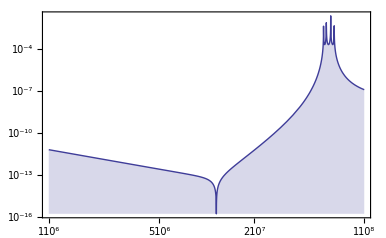

### Author

Jan G. Korvink © 2013, ..., 2 021

### Concept

This package facilitates the simulation of two-port networks. The design philosophy is as follows:

Specify: a circuit is specified using custom Mathematica heads. There are heads for primitive circuit elements such as resistors, inductances and capacitances, and combinations of elements in series or parallel, all of which are called objects. The primitive circuit elements are used to specify two-ports. Further specifications allow the interconnection of two-ports into circuits.

Verify: a circuit is checked for correctness by plotting it with the function CircuitGraphics[], which can handle two-ports as well as interconnections of two-ports, and by and CircuitCorrectQ[], which can check the correctness of interconnection.

Compute: a circuit can be converted into an expression using the functions CircuitExpression[] and NoiseExpression[]. Different representations are possible.

Manipulate: conversions are possible between various representations of the two-ports. Also, methodology is provided to generate two-ports from nodal analysis models.

Analyse: a circuit can be simulated. Its properties can be determined.

Complement: for example, the impedance matching network of a circuit can be computed.

Embed: a circuit can be embedded in another representation, for example, a  netlist can be generated with Netlist[].

### Usage

This gets the package:
fileName=StringJoin[NotebookDirectory[],”TwoPort.m”];
Get[fileName]

This lists the functions:
Names[“Twoport`*”]

### Todo features list:

+ How to make a balanced ABCD system? How to place items in the lower axis, so to speak?
+ Sources
+ Noise models
+ Stripline, and Cable twoport
+ Arbitrary networks
+ Circuit operators
+ Tidy up amplitude and phase
+ Netlist generation
+ Fixed size text in graphics (Scaled[] refers to the the entire plot range! Font size to the screen.
+ Plots: Nyquist (Transfer function, Im[] vs Re[], ω as parameter), Bode (dB of Power vs ω), Smith (Impedance Im[] vs Re[]), Root locus or Evans, Nichols or Black (|G(s)| vs Arg[G(s)]

#### DONE

+ Import 2 port models
+ Transistors
+ Smart evaluation and plotting of S-parameters.
+ Coupled inductor twoport (NO PLOT!)
+ Waveguide. 
+ Many conversions are missing.
+ Are the S-parameter conversions correctly implemented?

### References

1. Charles A. Desoer and Ernest S. Kuh, Basic Circuit Theory, McGraw-Hill, 1966
2. Wilfried Weißgerber, Elektrotechnik für Ingenieure 3, Vieweg 2007
3. K. C. Gupta, Peter S. Hall (Editors), Analysis and Design of Integrated Circuit Antenna Modules, Wiley Interscience, 1999
4. http://en.wikipedia.org/wiki/Electronic_filter_topology

## The package

### Package declaration.

```mathematica
BeginPackage["Twoport`"]
```

Twoport`

```mathematica
Off[InterpolatingFunction::dmval]
```

### Usage declarations. (Programmer: ADD NEW COMPONENTS, TWOPORTS, and INTERCONNECTIONS ELEMENTS HERE)

```mathematica
(* Simple manual *)
Twoport::usage="The package Twoport contains functions with which to model two-port circuits. Usage is straightforward if you follow the simple guidelines. \nYou first have to build up a circuit representation. Any of a number of predefined two-ports may be specified with the function heads whose names start with Twoport, i.e., a two-port π network is specified with TwoportPi[z1,z2,z3]. \nEach of the elements {z1,z2,z3} should be circuit element objects, i.e., they should have a head starting with Oneport, i.e. OneportCapacitor[c1]. The argument of the Oneports is usually either a number, here the capacitance, or a symbol that will be defined at a later stage. \nTwo-ports can be interconnected with functions whose heads start with Circuit, i.e., CircuitParallel[t1,t2] will interconnect the twoports t1 and t2 in parallel. \nOnce a circuit is completely defined, it can be plotted using the CircuitGraphics[c] function. The first argument is either a Circuit or a Twoport object.\nIf the circuit is correctly defined, you can obtain its two-port mathematica expression using CircuitExpression[c]. The result is a (2×2) matrix with a special header, the matrixA header, indicating that it is in the cascade format. \nYou can convert a two-port matrix between on of several representations, including impedance, admittance and the various hybrid formats. If the conversion is possible, you will obtain a (2×2) matrix with the appropriate head. Not all conversions make sense. \nA special conversion determines the s-parameters of your circuit. Fur this you have to also provide the input and output port conditions, typically a one-port specified by a simple impedance. \n\nPlease report any errors to korvink@imtek.uni-freiburg.de. Otherwise, happy simulating!";
```

```mathematica
(* Function that draws a two-port circuit *)
CircuitGraphics::usage="CircuitGraphics[tp,options] draws a graphical representation of its argument tp. The argument can be either a primitive two-port, or a circuit formed by joining an arbitrary number of two-ports. A Graphics[] object is returned. Options for Graphics[] can be specified.";
```

```mathematica
(* Function that converts a two-port circuit into an expression *)
CircuitExpression::usage="CircuitExpression[tp] computes a matrix representation of its argument tp. The argument can be either a primitive two-port, a compound two-port, or a circuit formed by joining an arbitrary number of two-ports.";

Amplitude::usage="Amplitude[z] produces the absolute value of its complex argument.";
Phase::usage="Phase[z] produces the angular value of its complex argument.";
```

```mathematica
(* Functions that define primitive circuit objects *)
OneportR::usage=OneportL::usage=OneportC::usage=OneportZ::usage=OneportShortedStub::usage=OneportOpenStub::usage=
OneportTerminatedStub::usage=OneportVS::usage=OneportCS::usage=OneportParallel::usage=OneportSeries::usage="The following primitive oneport circuit objects may be used:\n
\nOneportR[r] represents a resistor circuit element with a real-valued resistance r.
\nOneportL[l] represents an inductor circuit element with a real-valued inductance l.
\nOneportC[c] represents a capacitor circuit element with a real-valued capacitance c.
\nOneportZ[c] represents a symbolic element with a complex-valued capacitance Z. The user is responsible to include any frequency-dependent effects using the appropriate symbol.
\nOneportShortedStub[z0,β,l] represents a transmission line stub with one end short circuited, with an impedance z = ⅈ z0 Tan[βl], where  z0 is the characteristic impedance of the stub, β = 2π/λ is the phase constant of the stub, and l its length.
\nOneportOpenStub[z0,β,l] represents a transmission line stub with one end open circuit, with an impedance z = -ⅈ z0 Cot[βl], where z0 is the characteristic impedance of the stub, β = 2π/λ is the phase constant of the stub, and l its length.
\nOneportTerminatedStub[z0,xt,β,l] represents a transmission line stub with one end terminated by a reactance xt, with an impedance z = -ⅈ z0 Tan[βl+ArcTan[xt]], where z0 is the characteristic impedance of the stub, β = 2π/λ is the phase constant of the stub, and l its length.
\nOneportVS[v] represents a voltage source with amplitude v. The user is responsible to include any frequency-dependent effects using the appropriate symbol.
\nOneportCS[c] represents a current source with amplitude c. The user is responsible to include any frequency-dependent effects using the appropriate symbol.\n
\nPrimitive circuit objects may be rearranged in parallel or in series using:\n\n 
OneportParallel[a,b] represents the equivalent impedance of two parallel connected impedances a and b. Only use this to define the inner circuit of a single two-port element.
\nOneportSeries[a,b] represents the equivalent impedance of two series connected impedances a and b. Only use this to define the inner circuit of a single two-port element.";
```

```mathematica
OneportCImpedance::usage=OneportLImpedance::usage=OneportRImpedance::usage=OneportZImpedance::usage=OneportShortedStubImpedance::usage=OneportTerminatedStubImpedance::usage=OneportOpenStubImpedance::usage=OneportParallelImpedance::usage=OneportSeriesImpedance::usage="Oneport circuit primitives are used to specify two-ports. Their impedance values are calculated with these functions:\n\nOneportCImpedance[c,ω] defines the impedance of a capacitance of c Farad for a harmonic excitation at frequency ω s^-1. The result is complex valued.\nOneportLImpedance[l,ω] defines the impedance of an inductor of l Henry for a harmonic excitation at frequency ω s^-1. The result is complex valued.\nOneportRImpedance[r,ω] defines the impedance of a resistor of r Ohms. The result is real valued. The optional frequency is included for compatibility only.\nOneportParallelImpedance[z1,z2,...] forms the equivalent impedance of two or more parallel impedances.\nOneportSeriesImpedance[z1,z2,...] forms the equivalent impedance of two or more impedances in series.";
```

```mathematica
(* Functions that turn objects into two-ports *)
TwoportSeries::usage=TwoportSeriesABCD::usage="TwoportSeries[z] represents a two-port with a single series object z. Any of the Oneport* items may be used.\n\nTwoportSeriesABCD[z] creates an appropriate ABCD matrix. ABCD matrix entries are complex-valued.";
TwoportSeriesDown::usage=TwoportSeriesDownABCD::usage="TwoportSeriesDown[z] represents a two-port with a single series object z in the lower parallel branch. Any of the Oneport* items may be used.\n\nTwoportSeriesDownABCD[z] creates an appropriate ABCD matrix. ABCD matrix entries are complex-valued.";
TwoportShunt::usage=TwoportShuntABCD::usage="TwoportShunt[z] represents a two-port with a single shunted object z. Any of the Oneport* items may be used.\n\nTwoportShuntABCD[z] creates the ABCD matrix. ABCD matrix entries are complex-valued.";
TwoportLeftRight::usage=TwoportLeftRightABCD::usage="TwoportLeftRight[z1,z2] represents a two-port with with separate port impedances z1 and z2. Any of the Oneport* items may be used.\n\nTwoportLeftRightABCD[z1,z2] creates the ABCD matrix. ABCD matrix entries are complex-valued.";
TwoportGyrator::usage=TwoportGyratorABCD::usage="TwoportGyrator[α] represents a two-port gyrator element with gain α. This element can be used to mode the Hall effect, gyroscopic quantities, and any physics where a cross product appears. The gain α is the proportionality between the right port's current and the left port's voltage, and vice versa.\n\nTwoportGyratorABCD[α] creates the ABCD matrix. ABCD matrix entries are complex-valued.";
TwoportWaveguide::usage=TwoportWaveguideABCD::usage="TwoportWaveguide[z0,β,l] defines a section of lossless transmission line of physical length l and impedance z0. The phase constant is defined with the real number β, so that β l is the electrical length or phase shift of the waveguide.\n\nTwoportWaveguideABCD[z0,β,l] creates the ABCD matrix. ABCD matrix entries are complex-valued.";
TwoportLossyWaveguide::usage=TwoportLossyWaveguideABCD::usage="TwoportLossyWaveguide[z0,γ,l] defines a section of lossy transmission line of physical length l and impedance z0. The propagation constant is defined with the complex γ. When γ is purely complex, the waveguide is lossless.\n\nTwoportLossyWaveguide[z0,γ,l] creates the ABCD matrix. ABCD matrix entries are complex-valued.";
TwoportTransformer::usage=TwoportTransformerABCD::usage="TwoportTransformer[n] represents a twoport transformer with a windings ratio of n. The windings ratio should be a number.\n\nTwoportTransformerABCD[n] creates the ABCD matrix. ABCD matrix entries are complex-valued.";
TwoportPi::usage=TwoportPiABCD::usage="TwoportPi[z1,z2,z3] represents a two-port with three objects in a π network, with shunt impedances z1 and z3, and series impedance z2. Any of the Oneport* items may be used.\n\nTwoportPiABCD[z1,z2,z3] creates the ABCD matrix. ABCD matrix entries are complex-valued.";
TwoportTee::usage=TwoportTeeABCD::usage="TwoportTee[z1,z2,z3] represents a two-port with three objects in a τ network, with series impedances z1 and z3, and shunt impedance z2. Any of the Oneport* items may be used.\n\nTwoportTeeABCD[z1,z2] creates the ABCD matrix.";
TwoportInvert::usage=TwoportInvertABCD::usage="TwoportInvert[] flipps it's connections along the horizontal axis.\n\n TwoportInvertABCD[] creates the ABCD matrix.";
```

```mathematica
TwoportGammaI::usage=TwoportGammaIABCD::usage="TwoportGammaI[z1,z2] represents a two-port with two objects in a γ-I or left-half-t network. Any of the Oneport* items may be used.\n\nTwoportGammaIABCD[z1,z2] creates the ABCD matrix.";
TwoportGammaII::usage=TwoportGammaIIABCD::usage="TwoportGammaII[z1,z2] represents a two-port with two objects in a γ-II or right-half-t network. Any of the Oneport* items may be used.\n\nTwoportGammaIIABCD[z1,z2] creates the ABCD matrix.";
TwoportUnbalancedLadder::usage=TwoportUnbalancedLadderABCD::usage="TwoportUnbalancedLadder[z1,z2,n] of an unbalanced ladder network with n vertical branches and is not implemented yet.\n\nTwoportUnbalancedLadderABCD[z1,z2,n] creates the ABCD matrix ";
TwoportCoupledInductors::usage=TwoportCoupledInductorsABCD::usage="TwoportCoupledInductors[l1,l2,m] represents two coupled inductors with a mutual inductance m. l1 and l2 should be specified as inductors.\n\nTwoportCoupledInductors[l1,l2,m] creates the ABCD matrix.";
```

```mathematica
TwoportCsection::usage=TwoportCsectionABCD::usage="TwoportCsection[z1,z2] represents an unbalanced two-port C-network with one upper and lower impedance z1, and a shunt impedance z2.\n\nTwoportCsectionABCD[z1,z2] creates the ABCD matrix.";
TwoportHsection::usage=TwoportHsectionABCD::usage="TwoportHsection[z1,z2] represents an unbalanced two-port H-network with two upper and two lower series impedances z1, and a symmetrically placed shunt impedance z2.\n\nTwoportHsectionABCD[z1,z2] creates the ABCD matrix.";
TwoportBoxsection::usage=TwoportBoxsectionABCD::usage="TwoportBoxsection[z1,z2] represents an unbalanced two-port Box-network with one upper and one lower series impedance z1, and two symmetrically placed shunt impedances z2.\n\nTwoportBoxsectionABCD[z1,z2] creates the ABCD matrix.";
TwoportXsection::usage=TwoportXsectionABCD::usage="TwoportXsection[z1,z2] represents a symmetrical balanced two-port with two x-crossing impedances z1 and two parallel line impedances z2. It can e.g. be used to model a sheath wave blocker.\n\nTwoportXsectionABCD[z1,z2] creates the ABCD matrix.";
TwoportBalancedLadder::usage=TwoportBalancedLadderABCD::usage="TwoportBalancedLadder[z1,z2,n] represents yet.\n\nTwoportBalancedLadderABCD[z1,z2,n] creates the ABCD matrix.";
TwoportXsectionTee::usage=TwoportXsectionTeeABCD::usage="TwoportXsectionTee[z] represents a balanced ladder network with n vertical branches, and is not implemented yet.\n\nTwoportXsectionTeeABCD[z] creates the ABCD matrix.";
TwoportXsectionPi::usage=TwoportXsectionPiABCD::usage="TwoportXsectionPi[z1,z2] represents an unbalanced two-port X-network derived from a Π network, and is not implemented yet.\n\nTwoportXsectionPiABCD[z1,z2] creates the ABCD matrix.";
TwoportBridge::usage=TwoportBridgeABCD::usage="TwoportBridge[zl1,zl2,zr1,zr2] represents a balanced bridge network.\n\nTwoportBridgeABCD[z1,z2,r1,r2] creates the ABCD matrix.";
TwoportNPNce::usage=TwoportNPNceABCD::usage=TwoportNPNcb::usage=TwoportNPNcbABCD::usage=TwoportNPNcc::usage=TwoportNPNccABCD::usage=TwoportNMOScs::usage=TwoportNMOScsABCD::usage=TwoportNMOScg::usage=TwoportNMOScgABCD::usage=TwoportNMOScd::usage=TwoportNMOScdABCD::usage=TwoportMeasure::usage="Bipolar transistors and MOSFETs are specified as two-ports through an orientation and the relevant physical parameters. NPN bipolar transistors are physically by the three factors r_b, y_ce and b. NMOS FETS are specified by g_m, y_gs and y_ds. The three available orientations are common-emitter, common-base, and common-collector. For small signal analysis, there is no need for additional PNP or PMOS transistor models.\n\nTwoportNPNce[r_b,y_ce,b] represents a small signal NPN transistor in common emitter format. TwoportNPNceABCD[r_b,y_ce,b] creates the ABCD matrix.\nTwoportNPNcb[r_b,y_ce,b] represents a small signal NPN transistor in common emitter format. TwoportNPNcbABCD[r_b,y_ce,b] creates the ABCD matrix.\nTwoportNPNcc[r_b,y_ce,b] represents a small signal NPN transistor in common emitter format. TwoportNPNccABCD[r_b,y_ce,b] creates the ABCD matrix.\n\nTwoportNMOScs[g_m,y_gs,y_ds] represents a small signal NMOS transistor in common source format. TwoportNMOScsABCD[g_m,y_gs,y_ds] creates the ABCD matrix.\nTwoportNMOScg[g_m,y_gs,y_ds] represents a small signal NMOS transistor in common gate format. TwoportNMOScgABCD[g_m,y_gs,y_ds] creates the ABCD matrix.\nTwoportNMOScd[g_m,y_gs,y_ds] represents a small signal NMOS transistor in common drain format. TwoportNMOScdABCD[g_m,y_gs,y_ds] creates the ABCD matrix.\nTwoportMeasure[] is used to probe a two-port circuit. TwoportMeasureABCD[] creates an identity ABCD matrix.";
TwoportSwapTopBottom::usage="TwoportSwapTopBottom[m] swaps the role of the two terminals on each port of a two-port. Currently only works for matrixA matrices. This function is mainly used to generate specialised ABCD representations, such as balanced lines.";
```

```mathematica
NodalAdmittanceAssemble::usage="NodalAdmittanceAssemble[{{y,{node1,node2}}..}] is used to assemble an admittance matrix from one or more primitive components. The assumption is that the addmittance value y is inserted according to the two distinct nodal positions node1 and node2 using the stamp (GridBox[{{y,RowBox[{-,y}]},{RowBox[{-,y}],y}}]). If the node numbers lie outside of the range {1,4} a zero valued matrix is returned.";
```

```mathematica
matrixA::usage=matrixB::usage=matrixZ::usage=matrixY::usage=matrixH::usage=matrixP::usage=matrixS::usage=matrixT::usage="
The terminal behaviour of two-ports are captured by (2×2) matrices which can be in one of 6 formats:\n\nA, ABCD, or cascade matrices describe two-ports by (2×2) matrices that transform a right-hand voltage-current port to a left-hand voltage-current port. The matrixA head is a wrapper for the matrix.\nB, or inverse cascade matrices describe two-ports by (2×2) matrices that transform a right-hand voltage-current port to a left-hand voltage-current port. The matrixB head is a wrapper for the matrix.\nZ or impedance matrices describe the relation between currents and voltages on the ports, i.e., Ohm's law. Note that convention has the current at port 2 flowing into the two-port, which is the opposite convention as for ABCD matrices.\nY or dmittance matrices describe the relation between voltages and currents on the ports, i.e., the inverse Ohm law. Note that convention has the current at port 2 flowing into the two-port, which is the opposite convention as for ABCD matrices.\nH or hybrid matrices describe the relation between currents and voltages on the ports, i.e., Ohm's law. Note that convention has the current at port 2 flowing into the two-por, which is the opposite convention as for ABCD matrices.\nP or inverse hybrid matrices describe the relation between currents and voltages on the ports, i.e., Ohm's law. Note that convention has the current at port 2 flowing into the two-por, which is the opposite convention as for ABCD matrices.\nS or scattering-parameter matrices, and their inverses T, describe the relation between transmitted and reflected voltage waves on the ports.\n\nBy replacing any of the matrix heads with List, results in the matrix. This notebook overloads some basic operations such as Dot, Power and Inverse to also work for matrixA.";

NodalY::usage="Nodal admittance matrices can be used to describe a two-port circuit explicitly in terms of its 4 nodal voltages and currents. For further use, these should first be converted to twoport format, for example with the function NodalToTwoport.";
```

```mathematica
(* These are the conversions among 2-port representations *)
ToS::usage = ToT::usage = ToZ::usage = ToY::usage = ToH::usage = ToP::usage = ToA::usage = ToB::usage = "Two-ports can be interconverted with the following functions. Note that in all cases the optional source and load arguments are only required for conversion to and from S parameters, and if omitted, are set to 50 Ohms:\n\nToS[m,{zsource,zload}] produces the scatter matrix version of the two-port matrix representation m together with the source and load impedances. matrixS matrix entries are complex-valued.\nToZ[m] or ToZ[m,{zsource,zload}] produces the impedance matrix version of the two-port matrix representation m. matrixZ matrix entries are complex-valued.\nToY[m] or ToY[m,{zsource,zload}] produces the admittance matrix version of the two-port matrix representation m. matrixY matrix entries are complex-valued.\nToH[m] or ToH[m,{zsource,zload}] produces the hybrid matrix version of the two-port matrix representation m. matrixH matrix entries are complex-valued.\nToP[m] or ToP[m,{zsource,zload}] produces the inverse hybrid matrix version of the two-port matrix representation m. matrixP matrix entries are complex-valued.\nToA[m] or ToA[m,{zsource,zload}] produces the cascade matrix version of the two-port matrix representation m. matrixZ matrix entries are complex-valued.\nToB[m] or ToB[m,{zsource,zload}] produces the inverse cascade matrix version of the two-port matrix representation m. matrixZ matrix entries are complex-valued.";
```

```mathematica
(* Functions that form subcircuits from two-ports and other sub-circuits. *)
CircuitParallel::usage=CircuitCascade::usage=CircuitSerial::usage=CircuitHybrid::usage=CircuitInverseHybrid::usage="Two-ports are interconnected in special ways to again form two-ports, thereby allowing the construction of complex circuitry. The following functions facilitate this process:\n\nCircuitParallel[t1,t2] joins the subcircuits t1 and t2 such that both ports are in parallel. Sometimes called a parallel-parallel connection.\nTwoportCascade[t1,t2] cascades the subcircuits t1 and t2 .\nCircuitSerial[t1,t2] joins the subcircuits t1 and t2 such that both ports are in a serial configuration. Sometimes called a series-series connection.\nCircuitHybrid[t1,t2] joins the subcircuits t1 and t2 in a hybrid configuration, i.e., such that the left port is parallel and the right port in series. Sometimes called a parallel-series connection.\nCircuitInverseHybrid[t1,t2] joins the subcircuits t1 and t2 in an inverse hybrid configuration, i.e., such that the left port is in series and the right port in parallel. Sometimes called a series-parallel connection.";
```

```mathematica
GridArrangement::usage="GridArrangement is an option for LogLinearPlotSparameters, and controls whether the plots produced are a graphics grid or a list of plots.";

plotFunction::usage="plotFunction is an option for PlotSparameters with which to choose the kind of plotting function of each grid element.";

LogLinearPlotSparameters::usage=PlotSparameters::usage="PlotSparameters[s,{ω,ω0,ω1},opts] plots four graphs, namely the amplitudes |S_11|, |S_12|, and phases ∡|S_11| and ∡|S_12| for the specified frequency range. Optional plot parameters can also be specified.";
SmithPlot::usage="SmithPlot[f,{ω,ω0,ω1}] plots the function f, dependent on the frequency ω, on a Smith chart. The frequency is varied from ω0 to ω1. SmithPlot[{f_1,f_2,...},{ω,ω0,ω1}] does the same for a list of two or more functions f_1,f_2,...";
SolveABCD::usage="SolveABCD[m,p2] produces the vector result at port 1, of the vector signal from port 2, as modified by the ABCD matrix m. The argument p2 is hence a 2x1 vector containing the voltage across port 2, and the current flowing out of port 2. The result is a 2x1 vector representing the voltage across port 1 and the current flowing into port 1. The port voltages and currents are phasors and hence can be complex valued.";
SolveIntermediateABCD::usage="SolveIntermediateABCD[circuit,ω,p2] propagates the input vector p2 through all cascaded circuit ABCD matrices to provide a list of intermediate vectors between p2 and the output p1. Also see SolveABCD.";
PowerSolveABCD::usage="PowerSolveABCD[m,p2] first performs SolveABCD[m,p2], and then forms the product between the voltage and the current of the result, delivering the frequency-dependent power at the port. The port power is a phasor and hence can be complex valued.";
UnwrapPhase::usage="UnwrapPhase[data,tol,inc] takes a vector of phase data, and unwraps it. The optional arguments tol (= π) and inc (= 2π) steer the conversion process.";
NodalToTwoport::usage="NodalToTwoport[Yn,cv,ci] converts a (4×4) square admittance matrix Yn to a (2×2) two-port admittance matrix Yt. The conversion is controlled by two optional (2×4) constraint matrices. Per default, cv = (GridBox[{{1,0,RowBox[{-,1}],0},{0,1,0,RowBox[{-,1}]}}]) and ci = (GridBox[{{1,0,RowBox[{-,1}],0},{0,RowBox[{-,1}],0,1}}]). The matrix ci must have a pseudoinverse.";
```

```mathematica
(* The Mathematica symbols for the Touchstone file *)
Comment::usage=Version::usage=Optionline::usage=NumberOfPorts::usage=TwoPortDataOrder::usage=NumberOfFrequencies::usage=NumberOfNoiseFrequencies::usage=
Reference::usage=MixedModeOrder::usage=MatrixFormat::usage=NetworkData::usage=NoiseData::usage=Touchstone::usage="Two-ports are often defined by so-called touchstone files, which can be generated by measurement equipment for any two-port circuit or component. When such a file is imported into Mathematica, its entries are packed into symbols with similar names for easy extraction of the data. The data object for the file Touchstone[] will contain one or more of the following items: Comment[], Version[], Optionline[], NumberOfPorts[], TwoPortDataOrder[], NumberOfFrequencies[], NumberOfNoiseFrequencies[], Reference[], MixedModeOrder[], MatrixFormat[], NetworkData[], NoiseData[]";
```

```mathematica
(* Reading and generating a Touchstone file *)
ReadTouchstone::usage="ReadTouchstone[filepath] reads a Version 1 or Version 2 touchstone file and returns its contents as a Touchstone[] object.";
WriteTouchstone::usage="WriteTouchstone[{{f,mat}..},{{f,n1,n2,n3,n4}..}] writes a touchstone file based on the data provided. The data can consist of network and optional noise data. These data may be provided for one or more frequencies.";
ExtractTouchstoneNetwork::usage:="ExtractTouchstoneNetwork[ts] extracts a network twoport matrix from the Touchstone[] structure. Each of the four matrix entries are interpolation objects, and so can be plotted or algebraically combined with other twoports. Note that this will only work for 2 x 2 twoport structures.";
```

```mathematica
(* Rules for circuit conversion *)
OneportConversionRules::usage=TwoportConversionRules::usage=JoinConversionRules::usage="OneportConversionRules, TwoportConversionRules, and JoinConversionRules are rules used to convert a circuit expression to circuit equations. Normally these rules are used by the internal function CircuitExpression and are of no further concern. However, for partial numerical or sybolic evaluation of a circuit, for example of only the objects and twoports, but not the interconnection, in order to perform additional  manipulations, these rules are useful and hence provided here.";
AllTwoports::usage=AllTwoportsPattern::usage="AllTwoports gives the names of all the possible predefined twoport circuit elements. AllTwoportsPattern gives a pattern object for function calls and is exclusively used for programming. Use with care.";
AllOneports::usage=AllOneportsPattern::usage="AllOneports gives the names of all the possible predefined twoport circuit elements. AllOneportsPattern gives a pattern object for function calls and is exclusively used for programming.  Use with care.";
AllTwoportMatrices::usage=AllTwoportMatricesPattern::usage=CompleteTwoportMatrices::usage=CompleteTwoportMatricesPattern::usage="AllTwoportMatrices gives the names of all the possible predefined twoport matrices. CompleteTwoportMatrices adds the S and T matrices to the list. AllTwoportMatricesPattern and CompleteTwoportMatricesPattern gives a pattern object for function calls and is exclusively used for programming.  Use with care.";

DrawCompound::usage=DrawTwoport::usage="DrawCompound[] and DrawTwoport[] only here due to debugging.";
```

```mathematica
Begin["`Private`"];

Needs["Notation`"];
```

### Variables that describe all objects (Programmer: ADD NEW ONEPORTS, TWOPORTS, and INTERCONNECTION NAMES HERE)

```mathematica
(* The variables here allow us to cleanly define function prototypes that are often repeated in the code. *)

(* Currently, the sources are not included as oneports *)
AllOneports={OneportR,OneportL,OneportC,OneportZ,OneportShortedStub,OneportOpenStub,OneportTerminatedStub,OneportSeries,OneportParallel};
AllOneportsPattern=Alternatives@@(Blank[#]&/@AllOneports);

AllTwoportMatrices={matrixA,matrixB,matrixZ,matrixY,matrixH,matrixP};
AllTwoportMatricesPattern=Alternatives@@(Blank[#]&/@AllTwoportMatrices);
CompleteTwoportMatrices=Join[AllTwoportMatrices,{matrixS,matrixT}];
CompleteTwoportMatricesPattern=Alternatives@@(Blank[#]&/@CompleteTwoportMatrices);

AllTwoports={
TwoportSeries,
TwoportSeriesDown,
TwoportShunt,
TwoportLeftRight,
TwoportGyrator,
TwoportWaveguide,
TwoportLossyWaveguide,
TwoportTransformer,
TwoportInvert,
TwoportPi,
TwoportTee,
TwoportGammaI,
TwoportGammaII,
TwoportUnbalancedLadder,
TwoportCoupledInductors,
TwoportCsection,
TwoportHsection,
TwoportXsection,
TwoportBoxsection,
TwoportBalancedLadder,
TwoportXsectionTee,
TwoportXsectionPi,
TwoportBridge,
TwoportNPNce,
TwoportNPNcb,
TwoportNPNcc,
TwoportNMOScs,
TwoportNMOScg,
TwoportNMOScd,
TwoportMeasure
};

AllTwoportsPattern=Alternatives@@(Blank[#]&/@AllTwoports);
```

### ConversionRules (Programmer: ADD NEW ONEPORTS and INTERCONNECTION rules HERE): OneportConversionRules, TwoportConversionRules, JoinConversionRules

```mathematica
(* These rules form part of the circuit processing mechanism. *)
OneportConversionRules[ω_]:={
OneportC[c_]->OneportCImpedance[c,ω],OneportL[l_]->OneportLImpedance[l,ω],OneportR[r_]->OneportRImpedance[r],
OneportZ[z_]->OneportZImpedance[z],
OneportShortedStub[z0_,β_,l_]-> OneportShortedStubImpedance[z0,β,l,ω],
OneportOpenStub[z0_,β_,l_]-> OneportOpenStubImpedance[z0,β,l,ω],
OneportTerminatedStub[z0_,xt_,β_,l_]-> OneportTerminatedStubImpedance[z0,xt,β,l,ω],
OneportSeries[a_,b__]->OneportSeriesImpedance[a,b],
OneportParallel[a_,b_]->OneportParallelImpedance[a,b]
};

TwoportConversionRules=
(Rule[#,ToExpression[StringJoin[ToString[#],"ABCD"]]])&/@AllTwoports;

JoinConversionRules={
CircuitParallel[t1_,t2_]->ToA[ToY[t1]+ToY[t2]],
CircuitCascade[t1_,t2_]->Dot[ToA[t1],ToA[t2]],
CircuitCascade[t1_,t2_,t3__]->Dot[ToA[t1],CircuitCascade[t2,t3]],
CircuitSerial[t1_,t2_]->ToA[ToZ[t1]+ToZ[t2]],
CircuitHybrid[t1_,t2_]->ToA[ToH[t1]+ToH[t2]],
CircuitInverseHybrid[t1_,t2_]->ToA[ToP[t1]+ToP[t2]]
};

OnlyCascadeConversionRules={
CircuitParallel[t1_,t2_]->ToA[ToY[t1]+ToY[t2]],
CircuitCascade[t1_,CircuitCascade[t2__],t3__]->CircuitCascade[ToA[t1],t2,t3],
CircuitCascade[CircuitCascade[t1__],t2__]->CircuitCascade[t1,t2],
CircuitSerial[t1_,t2_]->ToA[ToZ[t1]+ToZ[t2]],
CircuitHybrid[t1_,t2_]->ToA[ToH[t1]+ToH[t2]],
CircuitInverseHybrid[t1_,t2_]->ToA[ToP[t1]+ToP[t2]]
};
```

### Notation for easier reading

```mathematica
Notation[^("A"){a__} ⟺ matrixA[a__]];
Notation[^("B"){a__} ⟺ matrixB[a__]];
Notation[^("Z"){a__} ⟺ matrixZ[a__]];
Notation[^("Y"){a__} ⟺ matrixY[a__]];
Notation[^("H"){a__} ⟺ matrixH[a__]];
Notation[^("P"){a__} ⟺ matrixP[a__]];
Notation[^("S"){a__} ⟺ matrixS[a__]];
Notation[^("T"){a__} ⟺ matrixT[a__]];
```

### Drawing a circuit diagram. (Programmer: ADD DIAGRAMS FOR NEW ONEPORTS, TWOPORTS, and INTERCONNECTIONS HERE): CircuitGraphics

#### Local, nonexported functions (ADD NEW COMPONENTS HERE)

```mathematica
(* A normalised two-port box lies in a bounding box square centred about the origin with a side length of 2. The actual box has a side length of 1.5. The ports lie 0.5 above and below the axis. *)

AbsLineThickness=1.0;

twoportBox[]:=Block[{b=1,h=.5,p=.75,q=.6,r=p-q},{EdgeForm[{AbsoluteThickness[AbsLineThickness],LightGray}],LightGray,Rectangle[{-p,-q},{p,q}],Rectangle[{-q,q},{q,p}],Rectangle[{-q,-q},{q,-p}],Disk[{-q,q},r],Disk[{-q,-q},r],Disk[{q,-q},r],Disk[{q,q},r],
AbsoluteThickness[AbsLineThickness],Red,Line[{{-b,h},{-p,h}}],Line[{{b,h},{p,h}}],Blue, Line[{{-b,-h},{-p,-h}}],Line[{{b,-h},{p,-h}}]}
];
```

```mathematica
(* A normalised through line connects the left to the right side of the two-port's box. When a component is present, the line is truncated. Vertical lines are shorter, as they connect to the two-port lines. *)
throughLine[]:={AbsoluteThickness[1],Line[{{-.75,0},{.75,0}}]};
horizontalComponentLine[]:={AbsoluteThickness[AbsLineThickness],Line[{{-.75,0},{-.375,0}}],Line[{{.375,0},{.75,0}}]};
verticalComponentLine[]:={AbsoluteThickness[AbsLineThickness],Line[{{0,doc},{0,-.375}}],Line[{{0,upc},{0,.375}}]};
```

```mathematica
(* The components fit in a bounding box that lie between -0.375 and 0.375 along the x-axis, and -.15 and .15 along the y axis. *)
resistorLine[]:={AbsoluteThickness[AbsLineThickness],Black,Line[{{-.375,0},{-.225,0},{-.15,-.15},{0,.15},{.15,-.15},{.225,0},{.375,0}}]};
inductorLine[]:={AbsoluteThickness[AbsLineThickness],Black,
Line[{{-.375,0},{-.225,.0}}],
Circle[{-0.150,0},.075,{0,Pi}],
Circle[{0,0},.075,{0,Pi}],
Circle[{0.150,0},.075,{0,Pi}],
Line[{{.375,0},{.225,.0}}]};
capacitorLine[]:={AbsoluteThickness[AbsLineThickness],Black,Line[{{-.375,0},{-.1,0}}],Rectangle[{-.1,-.15},{-.05,.15}],Rectangle[{.05,-.15},{.1,.15}],Line[{{.1,0},{.375,0}}]};
impedanceBox[]:={EdgeForm[AbsoluteThickness[AbsLineThickness]],GrayLevel[0.5],Rectangle[{-.375,-.075},{.375,.075}]};
openStubLine[]:={AbsoluteThickness[AbsLineThickness],Black,Line[{{-.375,0},{-.05,0},{-.05,-.05}}],{LightGray,EdgeForm[Black],Rectangle[{-.075,-.05},{-.025,-.25}],Rectangle[{.075,-.05},{.025,-.25}]},Black,Line[{{.375,0},{.05,0},{.05,-.05}}]};
shortStubLine[]:={openStubLine[],AbsoluteThickness[AbsLineThickness],Black,Circle[{0,-.25},.05,{0,-Pi}]};
terminatedStubLine[]:={openStubLine[],AbsoluteThickness[AbsLineThickness],Red,Circle[{0,-.25},.05,{0,-Pi}]};
voltagesourceDisk[]:={AbsoluteThickness[AbsLineThickness],Black,Line[{{-.375,0},{-.15,0}}],Line[{{.375,0},{.15,0}}],EdgeForm[AbsoluteThickness[AbsLineThickness]],LightGray,Disk[{0,0},.15],Black,Line[{{0,-.15},{0,.15}}]};
currentsourceDisk[]:={AbsoluteThickness[AbsLineThickness],Black,Line[{{-.375,0},{-.15,0}}],Line[{{.375,0},{.15,0}}],EdgeForm[AbsoluteThickness[AbsLineThickness]],LightGray,Disk[{0,0},.15],Black,Line[{{-.15,0},{.15,0}}]};
```

```mathematica
basicNPN[]:=Block[{s,e,c,r},
s={-0.075,0};e={-0.25,-.25};c=((e-s))/2;r=({{0, 1}, {-1, 0}}).c;
{AbsoluteThickness[AbsLineThickness],Black,Rectangle[{-.15,-.025},{.15,.025}],Line[{{0,0},{0,0.25}}],Line[{s,e}],Line[{{0.075,0},{.25,-.25}}],Polygon[{s+1.25c,s+.75c+.25r,s+.75c-.25r}]}
];
basicNMOS[]:=Block[{s,e,c,r},
s={-0.12,0};e={-0.12,-.25};c=((e-s))/2;r=({{0, 1}, {-1, 0}}).c;
{AbsoluteThickness[AbsLineThickness],Black,Rectangle[{-.15,-.025},{.15,.025}],Line[{{-.12,.05},{.12,.05}}],
Line[{{0,.05},{0,0.25}}],Line[{s,e}],Line[{{0.12,0},{.12,-.25}}],Polygon[{s+1.25c,s+.75c+.25r,s+.75c-.25r}]}
];
```

```mathematica
(* Drawing primitive objects. *)
DrawValue[h:(_OneportR|_OneportL|_OneportC|_OneportZ)[t_],c:{_,_}]:=Text[Style[ToString[t],FontColor->Blue,FontSlant->Italic,FontSize->10,FontFamily->"Courier"],c];
DrawValue[t_?NumberQ,c:{_,_}]:=Text[Style[ToString[t],FontColor->Blue,FontSlant->Italic,FontSize->10,FontFamily->"Courier"],c];
DrawValue[t_Symbol,c:{_,_}]:=Text[Style[SymbolName[t],FontColor->Blue,FontSlant->Italic,FontSize->10,FontFamily->"Courier"],c];
DrawValue[t_String,c:{_,_}]:=Text[Style[t,FontColor->Blue,FontSlant->Italic,FontSize->10,FontFamily->"Courier"],c];

DrawObject[o_?NumberQ]:={Red,Disk[{0,0},.05]};
DrawObject[o_Plus]:=DrawObject[Evaluate[o]];
DrawObject[o_Times]:=DrawObject[Evaluate[o]];
DrawObject[o_OneportR]:=resistorLine[];
DrawObject[o_OneportL]:=inductorLine[];
DrawObject[o_OneportC]:=capacitorLine[];
DrawObject[o_OneportZ]:=impedanceBox[];
DrawObject[o_OneportShortedStub]:=shortStubLine[];
DrawObject[o_OneportOpenStub]:=openStubLine[];
DrawObject[o_OneportTerminatedStub]:=terminatedStubLine[];
DrawObject[o_OneportVS]:=voltagesourceDisk[];
DrawObject[o_OneportCS]:=currentsourceDisk[];
DrawObject[OneportParallel[o1:AllOneportsPattern,o2:AllOneportsPattern]]:=Scale[{Translate[DrawObject[o1],{0,.25}],{AbsoluteThickness[AbsLineThickness],Line[{{-.375,.25},{-.875,.25},{-.875,-.25},{-.375,-.25}}],Line[{{.375,.25},{.875,.25},{.875,-.25},{.375,-.25}}]},Translate[DrawObject[o2],{0,-.25}]},0.375/0.875,{0,0}];
DrawObject[OneportSeries[o1:AllOneportsPattern,o2:AllOneportsPattern]]:=Scale[{Translate[DrawObject[o1],{-.5,0}],{AbsoluteThickness[AbsLineThickness],Line[{{-.125,0},{.125,0}}]},Translate[DrawObject[o2],{.5,0}]},0.375/0.875,{0,0}];
```

#### DrawTwoport (Programmer: ADD NEW ABCD ELEMENTS HERE)

```mathematica
upc=0.5;
doc=-0.5;
mic=0.0;
(* Draw two-port objects *)
DrawTwoport[TwoportSeries[o:AllOneportsPattern]]:={twoportBox[],{Blue,Translate[throughLine[],{0,doc}]},{Red,Translate[horizontalComponentLine[],{0,upc}]},Black,Translate[DrawObject[o],{0,upc}]};
```

```mathematica
DrawTwoport[TwoportSeriesDown[o:AllOneportsPattern]]:={twoportBox[],{Red,Translate[throughLine[],{0,upc}]},{Blue,Translate[horizontalComponentLine[],{0,doc}]},Translate[DrawObject[o],{0,doc}]};
```

```mathematica
DrawTwoport[TwoportShunt[o:AllOneportsPattern]]:={twoportBox[],{Blue,Translate[throughLine[],{0,doc}]},{Red,Translate[throughLine[],{0,upc}]},verticalComponentLine[],Rotate[DrawObject[o],-π/2,{0,0}]};
```

```mathematica
DrawTwoport[TwoportLeftRight[z1:AllOneportsPattern,
z2:AllOneportsPattern]]:={twoportBox[],
{AbsoluteThickness[AbsLineThickness],
{Red,Line[{{-.75,upc},{-.5,upc}}],
Line[{{.75,upc},{.5,upc}}]},
{Blue,Line[{{-.75,doc},{-.5,doc}}],
Line[{{.75,doc},{.5,doc}}]}},Translate[{verticalComponentLine[],Rotate[DrawObject[z1],-π/2,{0,0}]},{-.5,mic}],Translate[{verticalComponentLine[],Rotate[DrawObject[z2],-π/2,{0,0}]},{0.5,mic}]};
```

```mathematica
DrawTwoport[TwoportGyrator[α_]]:={twoportBox[],{Blue,Translate[horizontalComponentLine[],{0,doc}]},{Red,Translate[horizontalComponentLine[],{0,upc}]},AbsoluteThickness[AbsLineThickness],Line[{{-.375,upc},{-.375,doc}}],Line[{{.375,upc},{.375,doc}}],Circle[{-.375,0},.2,{-Pi/2,Pi/2}],Circle[{.375,0},.2,{Pi/2,3Pi/2}],DrawValue[StringJoin["α = ",ToString[α],"\n"],{0,upc}]};
```

```mathematica
DrawTwoport[TwoportWaveguide[z0_,β_,length_]]:=
{twoportBox[],
AbsoluteThickness[AbsLineThickness],{Red,Translate[horizontalComponentLine[],{0,upc}],Line[{{-.375,upc},{-.375,.1},{.375,.1},{.375,upc}}]},{Blue,Translate[horizontalComponentLine[],{0,doc}],Line[{{-.375,doc},{-.375,-.1},{.375,-.1},{.375,doc}}]},
{LightGray,EdgeForm[Black],Rectangle[{-.25,-.125},{.25,-.075}],Rectangle[{-.25,.125},{.25,.075}]},
DrawValue[StringJoin["{z0,β,λ}=\n",ToString[z0],",",ToString[β],",",ToString[length]],{0,upc}]};
```

```mathematica
DrawTwoport[TwoportLossyWaveguide[z0_,β_,length_]]:=
{twoportBox[],
AbsoluteThickness[AbsLineThickness],{Red,Translate[horizontalComponentLine[],{0,upc}],Line[{{-.375,upc},{-.375,.1},{.375,.1},{.375,upc}}]},{Blue,Translate[horizontalComponentLine[],{0,doc}],Line[{{-.375,doc},{-.375,-.1},{.375,-.1},{.375,doc}}]},
DrawValue[StringJoin["z0 = ",ToString[z0]],{0,upc}],
DrawValue[StringJoin["β = ",ToString[β]],{0,0}],
DrawValue[StringJoin["length = ",ToString[length]],{0,doc}]};
```

```mathematica
DrawTwoport[TwoportTransformer[n_]]:={
twoportBox[],
Translate[{verticalComponentLine[],Rotate[inductorLine[],-π/2,{0,0}]},{-.15,0}],
Translate[{verticalComponentLine[],Rotate[inductorLine[],π/2,{0,0}]},{.15,0}],AbsoluteThickness[AbsLineThickness],
{Red,Line[{{-.75,upc},{-.15,upc}}],Line[{{.75,upc},{.15,upc}}]},{Blue,Line[{{-.75,doc},{-.15,doc}}],Line[{{.75,doc},{.15,doc}}]},
DrawValue[StringJoin[ToString[n],"\n"],{0,upc}]
};
```

```mathematica
DrawTwoport[TwoportPi[o1:AllOneportsPattern,o2:AllOneportsPattern,o3:AllOneportsPattern]]:={twoportBox[],
{Blue,Translate[throughLine[],{0,doc}]},{Red,Translate[horizontalComponentLine[],{0,upc}]},Translate[{verticalComponentLine[],Rotate[DrawObject[o1],-π/2,{0,0}]},{-.5,0}],Translate[DrawObject[o2],{0,upc}],Translate[{verticalComponentLine[],Rotate[DrawObject[o3],-π/2,{0,0}]},{0.5,0}]};
```

```mathematica
DrawTwoport[TwoportTee[o1:AllOneportsPattern,o2:AllOneportsPattern,o3:AllOneportsPattern]]:={twoportBox[],
{Blue,Translate[throughLine[],{0,doc}]},{Red,Translate[horizontalComponentLine[],{0,upc}]},
Translate[DrawObject[OneportSeries[o1,o3]],{0,upc}],verticalComponentLine[],Rotate[DrawObject[o2],-π/2,{0,0}]};
```

```mathematica
DrawTwoport[TwoportInvert[]]:=
{twoportBox[],
{Red,Translate[horizontalComponentLine[],{0,upc}]},
{Blue,Translate[horizontalComponentLine[],{0,doc}]},
AbsoluteThickness[AbsLineThickness],
Line[{{-.375,doc},{.375,upc}}],
Line[{{-.375,upc},{.375,doc}}]
};
```

```mathematica
DrawTwoport[TwoportGammaI[o2:AllOneportsPattern,o3:AllOneportsPattern]]:={twoportBox[],
{Blue,Translate[throughLine[],{0,doc}]},Translate[horizontalComponentLine[],{0,upc}],Translate[DrawObject[o2],{0,upc}],Translate[{verticalComponentLine[],Rotate[DrawObject[o3],-π/2,{0,0}]},{-.5,0}]};
```

```mathematica
DrawTwoport[TwoportGammaII[o2:AllOneportsPattern,o3:AllOneportsPattern]]:={twoportBox[],
{Blue,Translate[throughLine[],{0,doc}]},Translate[horizontalComponentLine[],{0,upc}],Translate[DrawObject[o2],{0,upc}],Translate[{verticalComponentLine[],Rotate[DrawObject[o3],-π/2,{0,0}]},{.5,0}]};
```

```mathematica
DrawTwoport[TwoportUnbalancedLadder[o2:AllOneportsPattern]]:={twoportBox[]};
```

```mathematica
DrawTwoport[TwoportCoupledInductors[OneportL[l1_],OneportL[l2_],OneportL[m_]]]:={twoportBox[],
{Blue,Translate[throughLine[],{0,doc}]},Translate[{verticalComponentLine[],Rotate[inductorLine[],-π/2,{0,0}]},{-.15,0}],
Translate[{verticalComponentLine[],Rotate[inductorLine[],π/2,{0,0}]},{.15,0}],AbsoluteThickness[AbsLineThickness],
{Red,
Line[{{-.75,upc},{-.15,upc}}],
Line[{{.75,upc},{.15,upc}}]
}
(*, {DrawValue[l1,{-.25,.25}],
DrawValue[l2,{.25,.25}],
DrawValue[m,{0,.6}]} *)
};
```

```mathematica
DrawTwoport[TwoportCsection[o1:AllOneportsPattern,o2:AllOneportsPattern]]:=
{twoportBox[],
{Blue,Translate[{horizontalComponentLine[],DrawObject[o1]},{0,doc}]},
{Red,Translate[{horizontalComponentLine[],DrawObject[o1]},{0,upc}]},
Translate[{verticalComponentLine[],Rotate[DrawObject[o2],-π/2,{0,0}]},{-.5,0}]};
```

```mathematica
DrawTwoport[TwoportHsection[o1:AllOneportsPattern,o2:AllOneportsPattern]]:=
{twoportBox[],
{Blue,Translate[horizontalComponentLine[],{0,doc}]},
{Red,Translate[horizontalComponentLine[],{0,upc}]},Translate[DrawObject[OneportSeries[o1,o1]],{0,upc}],
Translate[DrawObject[OneportSeries[o1,o1]],{0,doc}],
verticalComponentLine[],Rotate[DrawObject[o2],-π/2,{0,0}]};
```

```mathematica
DrawTwoport[TwoportBoxsection[o1:AllOneportsPattern,o2:AllOneportsPattern]]:=
{twoportBox[],
{Blue,Translate[{horizontalComponentLine[],DrawObject[o1]},{0,doc}]},
{Red,Translate[{horizontalComponentLine[],DrawObject[o1]},{0,upc}]},
Translate[{verticalComponentLine[],Rotate[DrawObject[o2],π/2,{0,0}]},{-.5,0}],Translate[{verticalComponentLine[],Rotate[DrawObject[o2],-π/2,{0,0}]},{.5,0}]};
```

```mathematica
DrawTwoport[TwoportXsection[o1:AllOneportsPattern,o2:AllOneportsPattern]]:={twoportBox[],
{Blue,Translate[{horizontalComponentLine[],DrawObject[o2]},{0,doc}]},
{Red,Translate[{horizontalComponentLine[],DrawObject[o2]},{0,upc}]},
Translate[{DrawObject[o1]},{.2,-.15}],
Translate[{DrawObject[o1]},{-.2,.15}],
AbsoluteThickness[AbsLineThickness],Line[{{-.575,.15},{-.575,doc}}],Line[{{.575,-.15},{.575,doc}}],
Line[{{.1,.15},{.5,.15},{.5,upc}}],Line[{{-.1,-.15},{-.5,-.15},{-.5,upc}}]};
```

```mathematica
DrawTwoport[TwoportBalancedLadder[o2:AllOneportsPattern]]:={twoportBox[]};
```

```mathematica
DrawTwoport[TwoportXsectionTee[o2:AllOneportsPattern]]:={twoportBox[]};
```

```mathematica
DrawTwoport[TwoportXsectionPi[o2:AllOneportsPattern]]:={twoportBox[]};
```

```mathematica
DrawTwoport[TwoportBridge[z1:AllOneportsPattern,z2:AllOneportsPattern,r1:AllOneportsPattern,r2:AllOneportsPattern]]:=
{twoportBox[],
Translate[{verticalComponentLine[],Rotate[DrawObject[OneportSeries[z1,z2]],-π/2,{0,0}]},{-.25,0}],
Translate[{verticalComponentLine[],Rotate[DrawObject[OneportSeries[r1,r2]],-π/2,{0,0}]},{.25,0}],{AbsoluteThickness[AbsLineThickness],
{Red,Line[{{-.75,upc},{.25,upc}}]},
{Blue,Line[{{-.75,doc},{.25,doc}}]},
Black,
Line[{{-.25,0},{0,0},{0,0.6},{0.5,0.6},{0.5,upc},{.75,upc}}],Line[{{.25,0},{.5,0},{.5,doc},{.75,doc}}]}
};
```

```mathematica
DrawTwoport[TwoportNPNce[n1_,n2_,n3_]]:=
{AbsoluteThickness[AbsLineThickness],Black,
twoportBox[],
Rotate[basicNPN[],π/2.,{0,0}],
Line[{{-.25,0},{-.25,upc},{-.75,upc}}],
Line[{{.25,.25},{.25,upc},{.75,upc}}],
Line[{{.25,-.25},{.25,doc}}],
Translate[throughLine[],{0,doc}]
};
DrawTwoport[TwoportNPNcb[n1_,n2_,n3_]]:=
{AbsoluteThickness[AbsLineThickness],Black,
twoportBox[],
Rotate[basicNPN[],1.π,{0,0}],
Line[{{-.25,.25},{-.25,upc},{-.75,upc}}],
Line[{{.25,.25},{.25,upc},{.75,upc}}],
Line[{{0,-.25},{0,doc}}],
Translate[throughLine[],{0,doc}]
};
DrawTwoport[TwoportNPNcc[n1_,n2_,n3_]]:=
{AbsoluteThickness[AbsLineThickness],Black,
twoportBox[],
Scale[Rotate[basicNPN[],π/2.,{0,0}],{1,-1},{0,0}],
Line[{{-.25,0},{-.25,upc},{-.75,upc}}],
Line[{{.25,.25},{.25,upc},{.75,upc}}],
Line[{{.25,-.25},{.25,doc}}],
Translate[throughLine[],{0,doc}]
};

DrawTwoport[TwoportNMOScs[n1_,n2_,n3_]]:=
{AbsoluteThickness[AbsLineThickness],Black,
twoportBox[],
Rotate[basicNMOS[],π/2.,{0,0}],
Line[{{-.25,0},{-.25,upc},{-.75,upc}}],
Line[{{.25,.12},{.25,upc},{.75,upc}}],
Line[{{.25,-.12},{.25,doc}}],
Translate[throughLine[],{0,doc}]
};
DrawTwoport[TwoportNMOScg[n1_,n2_,n3_]]:=
{AbsoluteThickness[AbsLineThickness],Black,
twoportBox[],
Scale[Rotate[basicNMOS[],1.π,{0,0}],{-1,1},{0,0}],
Line[{{-.12,.25},{-.12,upc},{-.75,upc}}],
Line[{{.12,.25},{.12,upc},{.75,upc}}],
Line[{{0,-.25},{0,doc}}],
Translate[throughLine[],{0,doc}]
};
DrawTwoport[TwoportNMOScd[n1_,n2_,n3_]]:=
{AbsoluteThickness[AbsLineThickness],Black,
twoportBox[],
Scale[Rotate[basicNMOS[],π/2.,{0,0}],{1,-1},{0,0}],
Line[{{-.25,0},{-.25,upc},{-.75,upc}}],
Line[{{.25,.12},{.25,upc},{.75,upc}}],
Line[{{.25,-.12},{.25,doc}}],
Translate[throughLine[],{0,doc}]
};
```

```mathematica
(* Draw two-port objects *)
DrawTwoport[TwoportMeasure[]]:={
twoportBox[],Translate[throughLine[],{0,upc}],Translate[throughLine[],{0,doc}],
DrawValue["?",{0,0}]
};
```

#### DrawCompound (Programmer: ADD NEW INTERCONNECTIONS HERE)

```mathematica
(* When two-ports are combined to circuits, the bounding box of a hierarchy changes. This must be taken care of. Hence we use a new function, and add wrappers for simple two-ports. The user cannot access these functions. DrawCompound returns a pucture and data. The data contains the bounding box, and the position of the two ports. *)
DrawCompound[(h:AllTwoportsPattern)]:=Block[{},(*Print["DrawCompound: ",h];*)
Return[{DrawTwoport[h],{{{-1,-1},{1,1}},{{-1,0},{1,0}}}}]
];
```

```mathematica
DrawCompound[CircuitSerial[t1_,t2_]]:=Block[{picture1,bottomleft1,topright1,port1left,port1right,picture2,bottomleft2,topright2,port2left,port2right,height1,width1,height2,width2,height,width,translate1,translate2,lu,ld,ru,rd,up,do,l,r,l1,l2,r1,r2},

{picture1,{{bottomleft1,topright1},{port1left,port1right}}}=DrawCompound[t1];
{picture2,{{bottomleft2,topright2},{port2left,port2right}}}=DrawCompound[t2];

{width1,height1}=topright1-bottomleft1;
{width2,height2}=topright2-bottomleft2;
height=height1+height2;
width=Max[width1,width2];
translate1=-bottomleft1+{-width1/2,height/2-height1};
translate2=-bottomleft2+{-width2/2,-height/2};

(* left and right ports *)
l={-width/2-0.25,0};
r={width/2+0.25,0};
(* relative translation for the wires *)
up={0,.5};
do={0,-.5};
(* wire ends *)
lu= l+{.15,0}+up;
ld= l+{.15,0}+do;
ru= r-{.15,0}+up;
rd= r-{.15,0}+do;
(* component ports *)
l2=port2left+translate2;
l1=port1left+translate1;
r2=port2right+translate2;
r1=port1right+translate1;

{{Translate[picture1,translate1],
Translate[picture2,translate2],AbsoluteThickness[AbsLineThickness],
{Red,
Line[{l+up,lu}],
Line[{lu,l1+up}],
Line[{r+up,ru}],
Line[{ru,r1+up}]
},
{Blue,
Line[{l+do,ld}],
Line[{ld,l2+do}],
Line[{r+do,rd}],
Line[{rd,r2+do}]
},
Line[{l1+do,l2+up}],
Line[{r1+do,r2+up}]
},
{{{-width/2-0.25,-height/2},{width/2+0.25,height/2}},{l,r}}}
];
```

```mathematica
DrawCompound[CircuitInverseHybrid[t1_,t2_]]:=Block[{picture1,bottomleft1,topright1,port1left,port1right,picture2,bottomleft2,topright2,port2left,port2right,height1,width1,height2,width2,height,width,translate1,translate2,lu,ld,ru,rd,up,do,l,r,l1,l2,r1,r2},

{picture1,{{bottomleft1,topright1},{port1left,port1right}}}=DrawCompound[t1];
{picture2,{{bottomleft2,topright2},{port2left,port2right}}}=DrawCompound[t2];

{width1,height1}=topright1-bottomleft1;
{width2,height2}=topright2-bottomleft2;
height=height1+height2;
width=Max[width1,width2];
translate1=-bottomleft1+{-width1/2,height/2-height1};
translate2=-bottomleft2+{-width2/2,-height/2};

(* left and right ports *)
l={-width/2-0.25,0};
r={width/2+0.25,0};
(* relative translation for the wires *)
up={0,.5};
do={0,-.5};
(* wire ends *)
lu= l+{.15,0}+up;
ld= l+{.15,0}+do;
ru= r-{.15,0}+up;
rd= r-{.15,0}+do;
(* component ports *)
l2=port2left+translate2;
l1=port1left+translate1;
r2=port2right+translate2;
r1=port1right+translate1;

{{Translate[picture1,translate1],
Translate[picture2,translate2],AbsoluteThickness[AbsLineThickness],
{Red,
Line[{l+up,lu}],
Line[{lu,l1+up}],
Line[{lu,l2+up}],
Line[{r+up,ru}],
Line[{ru,r1+up}]
},
{Blue,
Line[{l+do,ld}],
Line[{ld,l2+do}],
Line[{ld,l1+do}],
Line[{r+do,rd}],
Line[{rd,r2+do}]
},
Line[{r1+do,r2+up}]
},
{{{-width/2-0.25,-height/2},{width/2+0.25,height/2}},{l,r}}}
]
```

```mathematica
DrawCompound[CircuitHybrid[t1_,t2_]]:=Block[{picture1,bottomleft1,topright1,port1left,port1right,picture2,bottomleft2,topright2,port2left,port2right,height1,width1,height2,width2,height,width,translate1,translate2,lu,ld,ru,rd,up,do,l,r,l1,l2,r1,r2},

{picture1,{{bottomleft1,topright1},{port1left,port1right}}}=DrawCompound[t1];
{picture2,{{bottomleft2,topright2},{port2left,port2right}}}=DrawCompound[t2];

{width1,height1}=topright1-bottomleft1;
{width2,height2}=topright2-bottomleft2;
height=height1+height2;
width=Max[width1,width2];
translate1=-bottomleft1+{-width1/2,height/2-height1};
translate2=-bottomleft2+{-width2/2,-height/2};

(* left and right ports *)
l={-width/2-0.25,0};
r={width/2+0.25,0};
(* relative translation for the wires *)
up={0,.5};
do={0,-.5};
(* wire ends *)
lu= l+{.15,0}+up;
ld= l+{.15,0}+do;
ru= r-{.15,0}+up;
rd= r-{.15,0}+do;
(* component ports *)
l2=port2left+translate2;
l1=port1left+translate1;
r2=port2right+translate2;
r1=port1right+translate1;

{{Translate[picture1,translate1],
Translate[picture2,translate2],AbsoluteThickness[AbsLineThickness],
{Red,
Line[{l+up,lu}],
Line[{lu,l1+up}],
Line[{r+up,ru}],
Line[{ru,r1+up}],
Line[{ru,r2+up}]
},
{Blue,
Line[{l+do,ld}],
Line[{ld,l2+do}],
Line[{r+do,rd}],
Line[{rd,r2+do}],
Line[{rd,r1+do}]
},
Line[{l1+do,l2+up}]
},
{{{-width/2-0.25,-height/2},{width/2+0.25,height/2}},{l,r}}}
];
```

```mathematica
DrawCompound[CircuitCascade[t1_,t2_]]:=Block[{picture1,bottomleft1,topright1,port1left,port1right,picture2,bottomleft2,topright2,port2left,port2right,height1,width1,height2,width2,height,width,translate1,translate2},

{picture1,{{bottomleft1,topright1},{port1left,port1right}}}=DrawCompound[t1];
{picture2,{{bottomleft2,topright2},{port2left,port2right}}}=DrawCompound[t2];

{width1,height1}=topright1-bottomleft1;
{width2,height2}=topright2-bottomleft2;
width=width1+width2;
height=Max[height1,height2];

translate1=-bottomleft1+{-width/2,-height1/2};
translate2=-bottomleft2+{width/2-width2,-height2/2};

Return[{
{Translate[picture1,translate1],
Translate[picture2,translate2]
},
{{{-width/2,-height/2},{width/2,height/2}},{{-width/2,0},{width/2,0}}}
}]
];
DrawCompound[CircuitCascade[t1_,t2_,t3__]]:=DrawCompound[CircuitCascade[t1,CircuitCascade[t2,t3]]];
```

```mathematica
DrawCompound[CircuitParallel[t1_,t2_]]:=Block[{picture1,bottomleft1,topright1,port1left,port1right,picture2,bottomleft2,topright2,port2left,port2right,height1,width1,height2,width2,height,width,translate1,translate2,lu,ld,ru,rd,up,do,l,r,l1,l2,r1,r2},

{picture1,{{bottomleft1,topright1},{port1left,port1right}}}=DrawCompound[t1];
{picture2,{{bottomleft2,topright2},{port2left,port2right}}}=DrawCompound[t2];

{width1,height1}=topright1-bottomleft1;
{width2,height2}=topright2-bottomleft2;
height=height1+height2;
width=Max[width1,width2];
translate1=-bottomleft1+{-width1/2,height/2-height1};
translate2=-bottomleft2+{-width2/2,-height/2};

(* left and right ports *)
l={-width/2-0.25,0};
r={width/2+0.25,0};
(* relative translation for the wires *)
up={0,.5};
do={0,-.5};
(* wire ends *)
lu= l+{.15,0}+up;
ld= l+{.15,0}+do;
ru= r-{.15,0}+up;
rd= r-{.15,0}+do;
(* component ports *)
l2=port2left+translate2;
l1=port1left+translate1;
r2=port2right+translate2;
r1=port1right+translate1;

{{Translate[picture1,translate1],
Translate[picture2,translate2],AbsoluteThickness[AbsLineThickness],
{Red,
Line[{l+up,lu}],
Line[{lu,l1+up}],
Line[{lu,l2+up}],
Line[{r+up,ru}],
Line[{ru,r1+up}],
Line[{ru,r2+up}]
},
{Blue,
Line[{l+do,ld}],
Line[{ld,l2+do}],
Line[{ld,l1+do}],
Line[{r+do,rd}],
Line[{rd,r2+do}],
Line[{rd,r1+do}]
}
},
{{{-width/2-0.25,-height/2},{width/2+0.25,height/2}},{l,r}}}
];
```

#### Exported function: CircuitGraphics

```mathematica
CircuitGraphics[o_,opts:OptionsPattern[]]:=Block[{},

(*Print["CircuitGraphics: ",o];
Print["DrawCompound[o]: ",DrawCompound[o]];
Print["Information[DrawCompound]: ";Information[DrawCompound]];*)


Graphics[DrawCompound[o][[1]],FilterRules[{opts}, Options[Graphics]]]
];
```

### Basic oneport element definitions. (Programmer: ADD NEW ONEPORTS HERE): Oneport ... Impedance

```mathematica
OneportCImpedance[c_,Ω_]:=1/(ⅈ Ω c);
OneportLImpedance[l_,Ω_]:=ⅈ Ω l;
OneportRImpedance[r_]:=r;
OneportZImpedance[z_]:=z;
OneportShortedStubImpedance[z0_,β_,l_,Ω_]:=(ⅈ z0 Ω Tan[β l]);OneportOpenStubImpedance[z0_,β_,l_,Ω_]:=(-ⅈ z0 Ω Cot[β l]);OneportTerminatedStubImpedance[z0_,xt_,β_,l_,Ω_]:=(ⅈ z0 Ω Tan[β l+ArcTan[xt]]);
```

```mathematica
(* These are not yet defined or active *)
OneportVoltageSource
OneportCurrentSource
```

```mathematica
OneportParallelImpedance[za_,zb_]:=1/(1/za+1/zb);
OneportParallelImpedance[za_,zb_,zc__]:=OneportParallelImpedance[za,OneportParallelImpedance[zb,zc]];
```

```mathematica
OneportSeriesImpedance[za_,zb_]:=za+zb;
OneportSeriesImpedance[za_,zb_,zc__]:=OneportSeriesImpedance[za,OneportSeriesImpedance[zb,zc]];
```

### Overloaded operations: Dot, MatrixPower, Inverse, MatrixForm, Plus

#### Overloaded operations for ABCD matrices.

```mathematica
Unprotect[Dot,MatrixPower,Inverse,MatrixForm, Plus];
Dot[first_matrixA,second__matrixA]:=matrixA@@Dot@@((List@@#)&/@{first,second});
Dot[a_?NumberQ first_matrixA,second__matrixA]:=a Dot[first,second];
Dot[first_matrixA,a_?NumberQ second__matrixA]:=a Dot[first,second];
Dot[a_?NumberQ +first_matrixA,second__matrixA]:= a second+Dot[first,second];
Dot[first_matrixA,a_?NumberQ +second__matrixA]:=Dot[first,second]+a first;
Dot[a_?NumberQ first_matrixA,b_?NumberQ second__matrixA]:=a b Dot[first,second];
Dot[a_?+NumberQ first_matrixA,b_?+NumberQ second__matrixA]:=a b+a second+b first+Dot[first,second];

Dot[first_matrixB,second__matrixB]:=matrixB@@Dot@@((List@@#)&/@{first,second});
Dot[a_?NumberQ first_matrixB,second__matrixB]:=a Dot[first,second];
Dot[first_matrixB,a_?NumberQ second__matrixB]:=a Dot[first,second];
Dot[a_?NumberQ +first_matrixB,second__matrixB]:= a second+Dot[first,second];
Dot[first_matrixB,a_?NumberQ +second__matrixB]:=Dot[first,second]+a first;
Dot[a_?NumberQ first_matrixB,b_?NumberQ second__matrixB]:=a b Dot[first,second];
Dot[a_?+NumberQ first_matrixB,b_?+NumberQ second__matrixB]:=a b+a second+b first+Dot[first,second];

Dot[first_matrixZ,second__matrixZ]:=matrixZ@@Dot@@((List@@#)&/@{first,second});
Dot[a_?NumberQ first_matrixZ,second__matrixZ]:=a Dot[first,second];
Dot[first_matrixZ,a_?NumberQ second__matrixZ]:=a Dot[first,second];
Dot[a_?NumberQ +first_matrixZ,second__matrixZ]:= a second+Dot[first,second];
Dot[first_matrixZ,a_?NumberQ +second__matrixZ]:=Dot[first,second]+a first;
Dot[a_?NumberQ first_matrixZ,b_?NumberQ second__matrixZ]:=a b Dot[first,second];
Dot[a_?+NumberQ first_matrixZ,b_?+NumberQ second__matrixZ]:=a b+a second+b first+Dot[first,second];

Dot[first_matrixY,second__matrixY]:=matrixY@@Dot@@((List@@#)&/@{first,second});
Dot[a_?NumberQ first_matrixY,second__matrixY]:=a Dot[first,second];
Dot[first_matrixY,a_?NumberQ second__matrixY]:=a Dot[first,second];
Dot[a_?NumberQ +first_matrixY,second__matrixY]:= a second+Dot[first,second];
Dot[first_matrixY,a_?NumberQ +second__matrixY]:=Dot[first,second]+a first;
Dot[a_?NumberQ first_matrixY,b_?NumberQ second__matrixY]:=a b Dot[first,second];
Dot[a_?+NumberQ first_matrixY,b_?+NumberQ second__matrixY]:=a b+a second+b first+Dot[first,second];

Dot[first_matrixH,second__matrixH]:=matrixH@@Dot@@((List@@#)&/@{first,second});
Dot[a_?NumberQ first_matrixH,second__matrixH]:=a Dot[first,second];
Dot[first_matrixH,a_?NumberQ second__matrixH]:=a Dot[first,second];
Dot[a_?NumberQ +first_matrixH,second__matrixH]:= a second+Dot[first,second];
Dot[first_matrixH,a_?NumberQ +second__matrixH]:=Dot[first,second]+a first;
Dot[a_?NumberQ first_matrixH,b_?NumberQ second__matrixH]:=a b Dot[first,second];
Dot[a_?+NumberQ first_matrixH,b_?+NumberQ second__matrixH]:=a b+a second+b first+Dot[first,second];

Dot[first_matrixP,second__matrixP]:=matrixP@@Dot@@((List@@#)&/@{first,second});
Dot[a_?NumberQ first_matrixP,second__matrixP]:=a Dot[first,second];
Dot[first_matrixP,a_?NumberQ second__matrixP]:=a Dot[first,second];
Dot[a_?NumberQ +first_matrixP,second__matrixP]:= a second+Dot[first,second];
Dot[first_matrixP,a_?NumberQ +second__matrixP]:=Dot[first,second]+a first;
Dot[a_?NumberQ first_matrixP,b_?NumberQ second__matrixP]:=a b Dot[first,second];
Dot[a_?+NumberQ first_matrixP,b_?+NumberQ second__matrixP]:=a b+a second+b first+Dot[first,second];

Dot[first_matrixS,second__matrixS]:=matrixS@@Dot@@((List@@#)&/@{first,second});
Dot[a_?NumberQ first_matrixS,second__matrixS]:=a Dot[first,second];
Dot[first_matrixS,a_?NumberQ second__matrixS]:=a Dot[first,second];
Dot[a_?NumberQ +first_matrixS,second__matrixS]:= a second+Dot[first,second];
Dot[first_matrixS,a_?NumberQ +second__matrixS]:=Dot[first,second]+a first;
Dot[a_?NumberQ first_matrixS,b_?NumberQ second__matrixS]:=a b Dot[first,second];
Dot[a_?+NumberQ first_matrixS,b_?+NumberQ second__matrixS]:=a b+a second+b first+Dot[first,second];

Dot[first:(_matrixA|_matrixB|_matrixZ|_matrixY|_matrixH|_matrixP|_matrixS),v:{_,_}]:=Dot[List@@first,v];

MatrixPower[first_matrixA,n_]:=matrixA@@MatrixPower[(List@@first),n];
MatrixPower[first_matrixB,n_]:=matrixB@@MatrixPower[(List@@first),n];
MatrixPower[first_matrixZ,n_]:=matrixZ@@MatrixPower[(List@@first),n];
MatrixPower[first_matrixY,n_]:=matrixY@@MatrixPower[(List@@first),n];
MatrixPower[first_matrixH,n_]:=matrixH@@MatrixPower[(List@@first),n];
MatrixPower[first_matrixP,n_]:=matrixP@@MatrixPower[(List@@first),n];
MatrixPower[first_matrixS,n_]:=matrixS@@MatrixPower[(List@@first),n];
MatrixPower[first_NodalY,n_]:=NodalY@@MatrixPower[(List@@first),n];

Inverse[first_matrixA]:=matrixA@@Inverse[(List@@first)];
Inverse[first_matrixB]:=matrixB@@Inverse[(List@@first)];
Inverse[first_matrixY]:=matrixY@@Inverse[(List@@first)];
Inverse[first_matrixZ]:=matrixZ@@Inverse[(List@@first)];
Inverse[first_matrixH]:=matrixH@@Inverse[(List@@first)];
Inverse[first_matrixP]:=matrixP@@Inverse[(List@@first)];
Inverse[first_matrixS]:=matrixS@@Inverse[(List@@first)];
Inverse[first_NodalY]:=NodalY@@Inverse[(List@@first)];

MatrixForm[first_matrixA]:=MatrixForm[(List@@first)];
MatrixForm[first_matrixB]:=MatrixForm[(List@@first)];
MatrixForm[first_matrixZ]:=MatrixForm[(List@@first)];
MatrixForm[first_matrixY]:=MatrixForm[(List@@first)];
MatrixForm[first_matrixH]:=MatrixForm[(List@@first)];
MatrixForm[first_matrixP]:=MatrixForm[(List@@first)];
MatrixForm[first_matrixS]:=MatrixForm[(List@@first)];
MatrixForm[first_NodalY]:=MatrixForm[(List@@first)];

Plus[first_matrixA,second_matrixA]:=matrixA@@((List@@first)+List@@second);
Plus[first_matrixB,second_matrixB]:=matrixB@@((List@@first)+List@@second);
Plus[first_matrixZ,second_matrixZ]:=matrixZ@@((List@@first)+List@@second);
Plus[first_matrixY,second_matrixY]:=matrixY@@((List@@first)+List@@second);
Plus[first_matrixH,second_matrixH]:=matrixH@@((List@@first)+List@@second);
Plus[first_matrixP,second_matrixP]:=matrixP@@((List@@first)+List@@second);
Plus[first_matrixS,second_matrixS]:=matrixS@@((List@@first)+List@@second);
Plus[first_NodalY,second_NodalY]:=NodalY@@((List@@first)+List@@second);

Protect[Dot,MatrixPower,Inverse,MatrixForm];
```

#### Overloaded operations for Circuit elements.

```mathematica
Unprotect[Plus,Power,Times];
Plus[first_OneportR,second__OneportR]:=OneportR@@Plus@@((List@@#)&/@{first,second});
Plus[first_OneportL,second__OneportL]:=OneportL@@Plus@@((List@@#)&/@{first,second});
Plus[first_OneportC,second__OneportC]:=OneportC@@Plus@@((List@@#)&/@{first,second});

(*
Times[OneportR[o_],OneportR[p_]]:=OneportR[o p];
Times[OneportL[o_],OneportL[p_]]:=OneportL[o p];
Times[OneportC[o_],OneportC[p_]]:=OneportC[o p];

Times[o_?NumberQ,OneportR[p_]]:=OneportR[o p];
Times[o_?NumberQ,OneportL[p_]]:=OneportL[o p];
Times[o_?NumberQ,OneportC[p_]]:=OneportC[o p];

Times[OneportR[o_],p_?NumberQ]:=OneportR[o p];
Times[OneportL[o_],p_?NumberQ]:=OneportL[o p];
Times[OneportC[o_],p_?NumberQ]:=OneportC[o p];

Power[OneportR[o_],p_?NumberQ]:=OneportR[o^p];
Power[OneportL[o_],p_?NumberQ]:=OneportL[o^p];
Power[OneportC[o_],p_?NumberQ]:=OneportC[o^p];
*)
Protect[Plus,Power,Times];
```

### Basic twoport ABCD elements. (Programmer: ADD NEW ABCD ELEMENTS HERE): Twoport ... ABCD

```mathematica
(* We only define ABCD elements. All other versions are obtained via conversion functions. *)
```

```mathematica
(* Basic unbalanced networks *)
TwoportSeriesABCD[z_]:=matrixA[{1,z},{0,1}];

TwoportSeriesDownABCD[z_]:=matrixA[{1,-z},{0,1}];

TwoportShuntABCD[z_]:=matrixA[{1,0},{1/z,1}];

TwoportLeftRightABCD[z1_,z2_]:=matrixA[{z1,0},{0,z2}];

TwoportGyratorABCD[α_]:=matrixA[{0,α},{-1/α,0}];

TwoportInvertABCD[]:=matrixA[{0,1},{1,0}];

TwoportWaveguideABCD[z0_,β_,length_]:=matrixA[{Cos[β length],ⅈ z0 Sin[β length]},{ⅈ (1/z0) Sin[β length],Cos[β length]}];

TwoportLossyWaveguideABCD[z0_,γ_,length_]:=matrixA[{Cosh[γ length],ⅈ z0 Sinh[γ length]},{ⅈ (1/z0) Sinh[γ length],Cosh[γ length]}];

TwoportTransformerABCD[n_]:=matrixA[{n,0},{0,1/n}];

TwoportPiABCD[z1_,z2_,z3_]:=TwoportShuntABCD[z1].TwoportSeriesABCD[z2].TwoportShuntABCD[z3];

TwoportTeeABCD[z1_,z2_,z3_]:=TwoportSeriesABCD[z1].TwoportShuntABCD[z2].TwoportSeriesABCD[z3];
```

```mathematica
(* Composite unbalanced networks *)TwoportGammaIABCD[z1_,z2_]:=TwoportShuntABCD[z1].TwoportSeriesABCD[z2];

TwoportGammaIIABCD[z1_,z2_]:=TwoportSeriesABCD[z1].TwoportShuntABCD[z2];

TwoportUnbalancedLadderABCD[z1_,z2_,n_]:=TwoportSeriesABCD[z1].TwoportShuntABCD[2z2].MatrixPower[TwoportGammaIABCD[2z1,2z2],n-1].TwoportSeriesABCD[2z1].TwoportShuntABCD[z2];

TwoportCoupledInductorsABCD[z1_,z2_,m_]:=TwoportSeriesABCD[z1-m].TwoportShuntABCD[m].TwoportSeriesABCD[z2-m];
```

```mathematica
(* Composite balanced networks *)
TwoportCsectionABCD[z1_,z2_]:=CircuitCascade[CircuitParallel[TwoportSeries[z1],TwoportSeries[z1]],TwoportShunt[z2]]//.TwoportConversionRules//.JoinConversionRules;

TwoportHsectionABCD[z1_,z2_]:=CircuitCascade[CircuitParallel[TwoportSeries[z1],TwoportSeries[z1]],CircuitCascade[TwoportShunt[z2],CircuitParallel[TwoportSeries[z1],TwoportSeries[z1]]]]//.TwoportConversionRules//.JoinConversionRules;

TwoportBoxsectionABCD[z1_,z2_]:=CircuitCascade[TwoportShunt[z2],CircuitCascade[CircuitParallel[TwoportSeries[z1],TwoportSeries[z1]],TwoportShunt[z2]]]//.TwoportConversionRules//.JoinConversionRules;

TwoportXsectionABCD[z1_,z2_]:=matrixA[{(z1+z2)/(z1-z2),(2z1 z2)/(z1-z2)},{2/(z1-z2),(z1+z2)/(z1-z2)}];

TwoportBalancedLadderABCD[z1_,z2_,n_]:=matrixA[{1,0},{0,1}];

TwoportXsectionTeeABCD[z_]:=matrixA[{1,0},{0,1}];

TwoportXsectionPiABCD[z1_,z2_]:=matrixA[{1,0},{0,1}];

TwoportBridgeABCD[z1_,z2_,r1_,r2_]:=matrixA[{((r1+r2)(z1+z2))/(r1 z2-r2 z1),(r2 z2(r1+z1)+r1 z1(r2+z2))/(r1 z2-r2 z1)},{(r1+z1+r2+z2)/(r1 z2-r2 z1),((r1+z1)(r2+z2))/(r1 z2-r2 z1)}];

TwoportNPNceABCD[rbe_,b_,yce_]:=ToA[matrixH[{rbe,0},{b,yce}]];

TwoportNPNcbABCD[rbe_,b_,yce_]:=ToA[matrixY[{(1+b)/rbe+yce,-yce},{b/rbe-yce,yce}]];

TwoportNPNccABCD[rbe_,b_,yce_]:=ToA[matrixH[{rbe,1},{b+1,yce}]];

TwoportNMOScsABCD[ygs_,gm_,yds_]:=ToA[matrixY[{ygs,0},{gm,yds}]];

TwoportNMOScgABCD[ygs_,gm_,yds_]:=ToA[matrixY[{gm+ygs+yds,-yds},{-gm-yds,yds}]];

TwoportNMOScdABCD[ygs_,gm_,yds_]:=ToA[matrixY[{ygs,-ygs},{-gm-ygs,gm+ygs+yds}]];

TwoportMeasureABCD[]:=matrixA[{1,0},{0,1}];
```

### Conversions among matrix representations: ToA, ToB, ToZ, ToY, ToH, ToP

#### TwoportSwapTopBottom NOT SURE IF THIS IS CORRECT

```mathematica
(* This code was generated by the following operation which, by first converting an ABCD to Z, then to pre- and post-multiply by a swapping operation that reorders the top and bottom terminals, then:
(ToA[matrixZ@@(List[{0,1},{1,0}].(List@@ToZ[matrixA[{a,b},{c,d}]]).List[{0,1},{1,0}])])
*)
TwoportSwapTopBottom[matrixA[{a_,b_},{c_,d_}]]:=matrixA[{-d/(b c-a d),b/(b c-a d)},{c/(b c-a d),-a/(b c-a d)}];
```

#### ToA, ToB, ToZ, ToY, ToH, ToP

```mathematica
ConvertTwoport[(fromHead:(Alternatives@@((#)&/@AllTwoportMatrices)))[{k11_,k12_},{k21_,k22_}],toHead:(Alternatives@@((#)&/@AllTwoportMatrices))]:=
Block[{V1,V2,I1,I2,fromlhs,fromrhs,tolhs,torhs},
If[fromHead==toHead,Return[fromHead@@{{k11,k12},{k21,k22}}]];
(* Determine the meaning of the variables lhs and rhs, before and after *)
Switch[fromHead,
matrixA,{fromlhs={V1,I1},fromrhs={V2,I2}},
matrixB,{fromlhs={V2,I2},fromrhs={V1,I1}},
matrixZ,{fromlhs={V1,V2},fromrhs={I1,I2}},
matrixY,{fromlhs={I1,I2},fromrhs={V1,V2}},
matrixH,{fromlhs={V1,I2},fromrhs={I1,V2}},
matrixP,{fromlhs={I1,V2},fromrhs={V1,I2}}
];
Switch[toHead,
matrixA,{tolhs={V1,I1},torhs={V2,I2}},
matrixB,{tolhs={V2,I2},torhs={V1,I1}},
matrixZ,{tolhs={V1,V2},torhs={I1,I2}},
matrixY,{tolhs={I1,I2},torhs={V1,V2}},
matrixH,{tolhs={V1,I2},torhs={I1,V2}},
matrixP,{tolhs={I1,V2},torhs={V1,I2}}
];
(* Perform the conversion *)
toHead@@(Coefficient[(#[[2]]),torhs]&/@Flatten[Solve[fromlhs=={{k11,k12},{k21,k22}}.fromrhs,tolhs]])
];
```

```mathematica
ToA[m:CompleteTwoportMatricesPattern]:=ToA[m,{50,50}];
ToA[m:AllTwoportMatricesPattern,{zsource_,zload_}]:=Block[{a,b,c,d,tmp},
tmp=ConvertTwoport[Head[m]@@{{a,b},{c,d}},matrixA];
Simplify[tmp/.{a->m[[1,1]],b->m[[1,2]],c->m[[2,1]],d->m[[2,2]]}]
];

ToB[m:CompleteTwoportMatricesPattern]:=ToB[m,{50,50}];
ToB[m:AllTwoportMatricesPattern,{zsource_,zload_}]:=Block[{a,b,c,d,tmp},
tmp=ConvertTwoport[Head[m]@@{{a,b},{c,d}},matrixB];
Simplify[tmp/.{a->m[[1,1]],b->m[[1,2]],c->m[[2,1]],d->m[[2,2]]}]
];

ToZ[m:CompleteTwoportMatricesPattern]:=ToZ[m,{50,50}];
ToZ[m:AllTwoportMatricesPattern,{zsource_,zload_}]:=Block[{a,b,c,d,tmp},
tmp=ConvertTwoport[Head[m]@@{{a,b},{c,d}},matrixZ];
Simplify[tmp/.{a->m[[1,1]],b->m[[1,2]],c->m[[2,1]],d->m[[2,2]]}]
];

ToY[m:CompleteTwoportMatricesPattern]:=ToY[m,{50,50}];
ToY[m:AllTwoportMatricesPattern,{zsource_,zload_}]:=Block[{a,b,c,d,tmp},
tmp=ConvertTwoport[Head[m]@@{{a,b},{c,d}},matrixY];
Simplify[tmp/.{a->m[[1,1]],b->m[[1,2]],c->m[[2,1]],d->m[[2,2]]}]
];

ToH[m:CompleteTwoportMatricesPattern]:=ToH[m,{50,50}];
ToH[m:AllTwoportMatricesPattern,{zsource_,zload_}]:=Block[{a,b,c,d,tmp},
tmp=ConvertTwoport[Head[m]@@{{a,b},{c,d}},matrixH];
Simplify[tmp/.{a->m[[1,1]],b->m[[1,2]],c->m[[2,1]],d->m[[2,2]]}]
];

ToP[m:CompleteTwoportMatricesPattern]:=ToP[m,{50,50}];
ToP[m:AllTwoportMatricesPattern,{zsource_,zload_}]:=Block[{a,b,c,d,tmp},
tmp=ConvertTwoport[Head[m]@@{{a,b},{c,d}},matrixP];
Simplify[tmp/.{a->m[[1,1]],b->m[[1,2]],c->m[[2,1]],d->m[[2,2]]}]
];
```

#### ToS and back again

```mathematica
ToS[m_]:=ToS[m,{50,50}];
```

```mathematica
(* Here we follow Pozar Microwave Engineering 2nd edition 
p 205 for S parameters given arbitrary input and output impedances, and table 4.2 on page 211 for the conversion formulae from A to S matrices. *)

ToS[matrixA[{a_,b_},{c_,d_}],{z01_,z02_}]:=Block[{},
matrixS@@({{a +b/50-c 50-d,2(a d-b c)√(Re[z01]/Re[z02])},{2 √(Re[z02]/Re[z01]),-a+b/50-c 50+d }}/(a +b/50+c 50+d ))
];
(* Here we are lazy. We know how to convert to and from A, and how to turn A into S. *)
ToS[m_matrixB,{z01_,z02_}]:=ToS[ToA[m,{z01,z02}],{z01,z02}];
ToS[m_matrixZ,{z01_,z02_}]:=ToS[ToA[m,{z01,z02}],{z01,z02}];
ToS[m_matrixY,{z01_,z02_}]:=ToS[ToA[m,{z01,z02}],{z01,z02}];
ToS[m_matrixH,{z01_,z02_}]:=ToS[ToA[m,{z01,z02}],{z01,z02}];
ToS[m_matrixP,{z01_,z02_}]:=ToS[ToA[m,{z01,z02}],{z01,z02}];
ToS[m_matrixS,{_,_}]:=m;
ToS[m_matrixT,{_,_}]:=matrixS@@Inverse[List@@m];
```

```mathematica
(*ToA[matrixS[{s11_,s12_},{s21_,s22_}],{z01_,z02_}]:=matrixA@@Simplify[{{(z01*+s11 z01)(1-s22)+s12 s21 z01,(z01*+s11 z01)(z02*+s22 z02)-s12 s21 z01 z02},{(1-s11)(1-s22)-s12 s21,(1-s11)(z02*+s22 z02)+s12 s21 z02}}/(2 s21 √(Re[z01]Re[z02]))];*)

ToA[matrixS[{s11_,s12_},{s21_,s22_}],{z01_,z02_}]:=Block[{},
matrixA@@({{(1+s11)(1-s22)+s12 s21 ,50((1+s11)(1+s22)-s12 s21) },{(1/50)((1-s11)(1-s22)-s12 s21),(1-s11)(1+s22)+s12 s21 }}/(2 s21 √(Re[z01]/Re[z02])))
];
(* Here we are lazy again. We know how to convert S to A, and how to turn A into anything else. *)
ToB[m_matrixS,{z01_,z02_}]:=ToB[ToA[m,{z01,z02}],{z01,z02}];
ToZ[m_matrixS,{z01_,z02_}]:=ToZ[ToA[m,{z01,z02}],{z01,z02}];
ToY[m_matrixS,{z01_,z02_}]:=ToY[ToA[m,{z01,z02}],{z01,z02}];
ToH[m_matrixS,{z01_,z02_}]:=ToH[ToA[m,{z01,z02}],{z01,z02}];
ToP[m_matrixS,{z01_,z02_}]:=ToP[ToA[m,{z01,z02}],{z01,z02}];
```

#### ToT and back again

```mathematica
(* For conversions to T we are again lazy. We know that T is the inverse of S. So, we can easily turn T into S. And we know how to turn S into anything else. *)
ToT[m_]:=ToT[m,{50,50}];
ToT[m_matrixT,b__]:=m;
ToT[m_matrixS,{_,_}]:=Block[{a,b,c,d},
tmp=Inverse[{{a,b},{c,d}}];
matrixT@@(tmp/.{a->m[[1,1]],b->m[[1,2]],c->m[[2,1]],d->m[[2,2]]})
];
ToT[m:AllTwoportMatricesPattern,{z01_,z02_}]:=ToT[ToS[m,{z01,z02}],{z01,z02}];
```

```mathematica
ToA[m_matrixT,{z01_,z02_}]:=ToA[ToS[m,{z01,z02}],{z01,z02}];
ToB[m_matrixT,{z01_,z02_}]:=ToB[ToS[m,{z01,z02}],{z01,z02}];
ToZ[m_matrixT,{z01_,z02_}]:=ToZ[ToS[m,{z01,z02}],{z01,z02}];
ToY[m_matrixT,{z01_,z02_}]:=ToY[ToS[m,{z01,z02}],{z01,z02}];
ToH[m_matrixT,{z01_,z02_}]:=ToH[ToS[m,{z01,z02}],{z01,z02}];
ToP[m_matrixT,{z01_,z02_}]:=ToP[ToS[m,{z01,z02}],{z01,z02}];
```

#### NodalYToTwoportY

```mathematica
NodalAdmittanceAssemble[admittances:{{_,{_,_}}..}]:=Block[{yn={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},indices},
indices=Union[Flatten[(#[[2]])&/@admittances]];
If[Min[indices]<1||Max[indices]>4,Return[yn],
(Part[yn,#[[2,1]],#[[2,1]]]+=#[[1]])&/@admittances;
(Part[yn,#[[2,1]],#[[2,2]]]-=#[[1]])&/@admittances;
(Part[yn,#[[2,2]],#[[2,1]]]-=#[[1]])&/@admittances;
(Part[yn,#[[2,2]],#[[2,2]]]+=#[[1]])&/@admittances;
Return[NodalY@@yn]
];
];
```

```mathematica
NodalToTwoport[yn:NodalY[{_,_,_,_},{_,_,_,_},{_,_,_,_},{_,_,_,_}],cv:{{_,_,_,_},{_,_,_,_}}:({{1, 0, -1, 0}, {0, 1, 0, -1}}),ci:{{_,_,_,_},{_,_,_,_}}:({{1, 0, -1, 0}, {0, 1, 0, -1}})]:=matrixY@@(ci.(List@@yn).PseudoInverse[cv]);
```

#### Redundancies due to similarity or complimentarity

```mathematica
ToA[ToA[a_,b___],b___]:=ToA[a,b];
ToB[ToB[a_,b___],b___]:=ToB[a,b];
ToA[ToB[a_matrixA,b___],b___]:=a;
ToB[ToA[a_matrixB,b___],b___]:=a;
```

```mathematica
ToZ[ToZ[a_],b___]:=ToZ[a,b];
ToY[ToY[a_],b___]:=ToY[a,b];
ToZ[ToY[a_matrixZ,b___],b___]:=a;
ToY[ToZ[a_matrixY,b___],b___]:=a;
```

```mathematica
ToH[ToH[a_],b___]:=ToH[a,b];
ToP[ToP[a_],b___]:=ToP[a,b];
ToH[ToP[a_matrixH,b___],b___]:=a;
ToP[ToH[a_matrixP,b___],b___]:=a;
```

```mathematica
ToS[ToS[a_],b___]:=ToS[a,b];
ToT[ToT[a_],b___]:=ToT[a,b];
ToS[ToT[a_matrixS,b___],b___]:=a;
ToT[ToS[a_matrixT,b___],b___]:=a;
```

```mathematica
ToA[a_?NumberQ m:AllTwoportMatricesPattern,b___]:=a ToA[m,b];
ToB[a_?NumberQ m:AllTwoportMatricesPattern,b___]:=a ToB[m,b];
```

```mathematica
ToZ[a_?NumberQ m:AllTwoportMatricesPattern,b___]:=a ToA[m,b];
ToY[a_?NumberQ m:AllTwoportMatricesPattern,b___]:=a ToB[m,b];
```

```mathematica
ToH[a_?NumberQ,m:AllTwoportMatricesPattern,b___]:=a ToA[m,b];
ToP[a_?NumberQ,m:AllTwoportMatricesPattern,b___]:=a ToB[m,b];
```

### Converting a circuit to an expression: CircuitExpression

```mathematica
CircuitExpression[circuit_,ω_]:=(((circuit//.OneportConversionRules[ω])//.TwoportConversionRules)//.JoinConversionRules);
CircuitExpression[circuit_]:=Message[CircuitExpression::argx,1,2];

(* We need this function to eliminate all but cascades, so that we can propagate a solution through the cascaded circuit blocks. *)
OnlyCascadeExpression[circuit_,ω_]:=(((circuit//.OneportConversionRules[ω])//.TwoportConversionRules)//.OnlyCascadeConversionRules);
OnlyCascadeExpression[circuit_]:=Message[OnlyCascadeExpression::argx,1,2];
```

### Converting a circuit to an expression: CircuitExpression

### Solution process: SolveABCD, PowerSolveABCD, PlotABCD, PowerPlotABCD, PlotSparameters, LogLinearPlotSparameters, SmithPlot

```mathematica
SolveABCD[first_matrixA,port2:{rhsVoltage_,rhsCurrent_}]:=(List@@first).port2;
PowerSolveABCD[first_matrixA,port2:{rhsVoltage_,rhsCurrent_}]:=Times@@((List@@first).port2);
PlotABCD[first_matrixA,port2:{rhsVoltage_,rhsCurrent_},{Omega_Symbol,ostart_,oend_}]:=Plot[#,{Omega,ostart,oend},Axes->False,Frame->True,PlotRange->All]&/@Flatten[({Re[#],Im[#]}&/@Join[SolveABCD[first,port2],port2])];
PowerPlotABCD[first_matrixA,port2:{rhsVoltage_,rhsCurrent_},{Omega_Symbol,ostart_,oend_}]:=Plot[#,{Omega,ostart,oend},Axes->False,Frame->True,PlotRange->All]&/@Flatten[({Re[#],Im[#]}&/@List[PowerSolveABCD[first,port2],Times@@port2])];

SolveIntermediateABCD[circuit_,ω_,inputVector:{_,_}]:=Chop[FoldList[CircuitExpression[Dot[#2,#1],ω]&,inputVector,List@@circuit]];
```

```mathematica
Amplitude[s_]:=Abs[s];
Phase[s_]:=Block[{ff},ff=Arg[s]; While[ff<-π,ff+=2π];While[ff>π,ff-=2π];ff];
```

```mathematica
Options[PlotSparameters]:={GridArrangement->True,plotFunction->Plot};

PlotSparameters[s:matrixS[{s11_InterpolatingFunction,s12_InterpolatingFunction},{s21_InterpolatingFunction,s22_InterpolatingFunction}],{ω_Symbol,ω0_,ω1_},opts:OptionsPattern[]]:=PlotSparameters[matrixS[{s11[ω],s12[ω]},{s21[ω],s22[ω]}],{ω,ω0,ω1},opts];

PlotSparameters[s:matrixS[{s11_,s12_},{s21_,s22_}],{ω_Symbol,ω0_,ω1_},opts:OptionsPattern[]]:=Block[{options,op,g={},fscaling=1.,flabel="Hz",fxticks,phaseticks,amplitudeticks,gridarrangement,f0,f1,f0s,f1s,plotfunction},

(* because of the way we define impedances, we use angular frequencies. However, in plots, we like to use real frequency units. First, we convert the plot limits. *)
f0=ω0/2./π;
f1=ω1/2./π;

(* Next, we want to tidy up the scale factor, to have either Hz, kHz, MHz, GHz, or THz *)
Switch[Floor[RealExponent[f1],3],0,flabel="Hz",3,flabel="kHz",6,flabel="MHz",9,flabel="GHz",12,flabel="THz"];
fscaling=10^Floor[RealExponent[f1],3];

f0s=f0/fscaling;
f1s=f1/fscaling;

fxticks=FindDivisions[{f0s,f1s},2];
phaseticks={{-π,0,π},None};
amplitudeticks={Automatic,None};

gridarrangement=((GridArrangement/.{opts})/.Options[PlotSparameters]);
plotfunction=((plotFunction/.{opts})/.Options[PlotSparameters]);

op=Options[plotfunction];

SetOptions[Plot,{ Frame->True,Axes->False,Filling->Bottom,FrameLabel->flabel}];
SetOptions[Plot,FilterRules[op,{opts}]];
SetOptions[plotfunction,{ Frame->True,Axes->False,Filling->Bottom,FrameLabel->flabel}];
SetOptions[plotfunction,FilterRules[op,{opts}]];

g={{Plot[Amplitude[s[[1,1]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"|S_11|",FrameTicks->{{amplitudeticks,None},{fxticks,None}},PlotRange->{{f0s,f1s},All}],Plot[Amplitude[s[[1,2]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"|S_12|",FrameTicks->{{amplitudeticks,None},{fxticks,None}},PlotRange->{{f0s,f1s},All}],Plot[Amplitude[s[[2,1]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"|S_21|",FrameTicks->{{amplitudeticks,None},{fxticks,None}},PlotRange->{{f0s,f1s},All}],Plot[Amplitude[s[[2,2]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"|S_22|",FrameTicks->{{amplitudeticks,None},{fxticks,None}},PlotRange->{{f0s,f1s},All}]},{
Plot[Phase[s[[1,1]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"∡|S_11|",FrameTicks->{{amplitudeticks,None},{fxticks,None}},PlotRange->{{f0s,f1s},{-π,π}}],Plot[Phase[s[[1,2]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"∡|S_12|",FrameTicks->{{amplitudeticks,None},{fxticks,None}},PlotRange->{{f0s,f1s},{-π,π}}],Plot[Phase[s[[2,1]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"∡|S_21|",FrameTicks->{{amplitudeticks,None},{fxticks,None}},PlotRange->{{f0s,f1s},{-π,π}}],Plot[Phase[s[[2,2]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"∡|S_22|",FrameTicks->{{amplitudeticks,None},{fxticks,None}},PlotRange->{{f0s,f1s},{-π,π}}]}};

SetOptions[Plot,op];

If[gridarrangement,
Return[GraphicsGrid[g,ImageSize->Scaled[1]]],
Return[g]
]

];
```

```mathematica
Options[LogLinearPlotSparameters]:={GridArrangement->True};

LogLinearPlotSparameters[s:matrixS[{s11_InterpolatingFunction,s12_InterpolatingFunction},{s21_InterpolatingFunction,s22_InterpolatingFunction}],{ω_Symbol,ω0_,ω1_},opts:OptionsPattern[]]:=LogLinearPlotSparameters[matrixS[{s11[ω],s12[ω]},{s21[ω],s22[ω]}],{ω,ω0,ω1},opts];

LogLinearPlotSparameters[s_matrixS,{ω_Symbol,ω0_,ω1_},opts:OptionsPattern[]]:=Block[{options,ollp,olllp,g,fscaling=1.,flabel="Hz",fxticks,phaseticks,amplitudeticks,gridarrangement,f0,f1,f0s,f1s},

(* because of the way we define impedances, we use angular frequencies. However, in plots, we like to use real frequency units. First, we convert the plot limits. *)
f0=ω0/2./π;
f1=ω1/2./π;

(* Next, we want to tidy up the scale factor, to have either Hz, kHz, MHz, GHz, or THz *)
Switch[Floor[RealExponent[f1],3],0,flabel="Hz",3,flabel="kHz",6,flabel="MHz",9,flabel="GHz",12,flabel="THz"];
fscaling=10^Floor[RealExponent[f1],3];

f0s=f0/fscaling;
f1s=f1/fscaling;

fxticks=FindDivisions[{f0s,f1s},2];
phaseticks={{-π,0,π},None};
amplitudeticks={Automatic,None};

gridarrangement=GridArrangement/.{opts}/.Options[LogLinearPlotSparameters];

ollp=Options[LogLogPlot];
olllp=Options[LogLinearPlot];

SetOptions[LogLogPlot,{ Frame->True,Filling->Bottom,FrameLabel->flabel,Ticks->None}];
SetOptions[LogLogPlot,FilterRules[ollp,{opts}]];

SetOptions[LogLinearPlot,{ Frame->True,Filling->Bottom,FrameLabel->flabel,Ticks->None}];
SetOptions[LogLinearPlot,FilterRules[olllp,{opts}]];

g={{LogLinearPlot[Amplitude[s[[1,1]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"|S_11|",FrameTicks->{{amplitudeticks,None},{fxticks,None}},PlotRange->{{f0s,f1s},All}],LogLinearPlot[Amplitude[s[[1,2]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"|S_12|",FrameTicks->{amplitudeticks,fxticks},PlotRange->{{f0s,f1s},All}],LogLinearPlot[Amplitude[s[[2,1]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"|S_21|",FrameTicks->{amplitudeticks,fxticks},PlotRange->{{f0s,f1s},All}],LogLinearPlot[Amplitude[s[[2,2]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"|S_22|",FrameTicks->{amplitudeticks,fxticks},PlotRange->{{f0s,f1s},All}]},{
LogLinearPlot[Phase[s[[1,1]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"∡|S_11|",FrameTicks->{phaseticks,fxticks},PlotRange->{{f0s,f1s},{-π,π}}],LogLinearPlot[Phase[s[[1,2]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"∡|S_12|",FrameTicks->{phaseticks,fxticks},PlotRange->{{f0s,f1s},{-π,π}}],LogLinearPlot[Phase[s[[2,1]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"∡|S_21|",FrameTicks->{phaseticks,fxticks},PlotRange->{{f0s,f1s},{-π,π}}],LogLinearPlot[Phase[s[[2,2]]]/.ω->(2π f fscaling),{f,f0s,f1s},PlotLabel->"∡|S_22|",FrameTicks->{phaseticks,fxticks},PlotRange->{{f0s,f1s},{-π,π}}]}};

SetOptions[LogLogPlot,ollp];
SetOptions[LogLinearPlot,olllp];

If[gridarrangement,
Return[GraphicsGrid[g,ImageSize->Scaled[1]]],
Return[g]
]
];
```

```mathematica
SmithChartGraphics :=Block[ {SmithR,SmithX,coordinateLines,rstyle,xstyle,rtextstyle,xtextstyle},

SmithR[r_, θ_]:={(Cos[θ]+r)/(1+r),Sin[θ]/(1+r)};
SmithX[x_, θ_]:={ Cos[θ]/x+1,(Sin[θ]+1)/x};

rstyle=Directive[GrayLevel[.7],Thickness[0.002](*,Dashing[.005]*)];
xstyle=Directive[GrayLevel[.7],Thickness[0.002](*,Dashing[.005]*)];
rtextstyle[t_String]:=Style[t,Black,6,FontFamily->"Helvetica"];
xtextstyle[t_String]:=Style[t,Black,6,FontFamily->"Helvetica"];

coordinateLines={
PolarPlot[1, {phi, 0, 2π}, 
		PlotStyle->rstyle,
		DisplayFunction->Identity],
 ParametricPlot[Evaluate[SmithR[1/2, θ]], {θ, 0, 2π},
		PlotStyle->rstyle,
		DisplayFunction->Identity],
 ParametricPlot[Evaluate[SmithR[1, θ]], {θ, 0, 2π},
		PlotStyle->rstyle,
		DisplayFunction->Identity],
 ParametricPlot[Evaluate[SmithR[2, θ]], {θ, 0, 2π},
		PlotStyle->rstyle,
		DisplayFunction->Identity],
 ParametricPlot[Evaluate[SmithX[2,θ]], {θ, 3π/2, 51π/64},
		PlotStyle->xstyle,
		DisplayFunction->Identity],
 ParametricPlot[Evaluate[SmithX[1,θ]], {θ, 3π/2, π},
		PlotStyle->xstyle,
		DisplayFunction->Identity],
ParametricPlot[Evaluate[SmithX[1/2,θ]], {θ, 3π/2, 617π/512},
		PlotStyle->xstyle,
		DisplayFunction->Identity],
 ParametricPlot[Evaluate[SmithX[-2,θ]], {θ, 13π/64, -π/2},
		PlotStyle->xstyle,
		DisplayFunction->Identity],
ParametricPlot[Evaluate[SmithX[-1,θ]], {θ, 0, -π/2},
		PlotStyle->xstyle,
		DisplayFunction->Identity],
 ParametricPlot[Evaluate[SmithX[-1/2,θ]], {θ, -105π/512, -π/2},
		PlotStyle->xstyle,
		DisplayFunction->Identity],
Graphics[{ xstyle, Line[{ {-1,0}, {1,0} }] }]
};

labels =Graphics[( Text@@#)&/@{
		{rtextstyle["R = 0"],{.35,1}},
		{rtextstyle["R = 0.5"],{.35,.7}},	
		{rtextstyle["R = 1.0"],{.5,.53}},
		{rtextstyle["R = 2.0"],{.67,.36}},
		{xtextstyle["X = -2.0"],{.75,-.85}},
		{xtextstyle["X = -1.0"],{0,-1.05}},
		{xtextstyle["X = -0.5"],{-.75,-.85}},
		{xtextstyle["X = 0"],{-1.1,0}},
		{xtextstyle["X = 2.0"],{.75,.85}},
		{xtextstyle["X = 1.0"],{0,1.05}},
		{xtextstyle["X = 0.5"],{-.75,.85}}}];

Show[labels, coordinateLines,
Axes->None,
AspectRatio->Automatic,
DisplayFunction->Identity]
    ];
SmithPlotSingle[f_,{ω_Symbol,ω1_?NumberQ,ω2_?NumberQ}]:=
Block[{newf,newx,newy},
newf=Evaluate[((f-50.)/(f+50.))];
newx=Re[newf];
newy=Im[newf];
ParametricPlot[{newx,newy},{ω,ω1,ω2}]
];
SmithPlot[f_,{ω_Symbol,ω1_?NumberQ,ω2_?NumberQ}]:=Show[{SmithChartGraphics,SmithPlotSingle[f,{ω,ω1,ω2}]}];
SmithPlot[fl:{f__},{ω_Symbol,ω1_?NumberQ,ω2_?NumberQ}]:=Show[{SmithChartGraphics,SmithPlotSingle[#,{ω,ω1,ω2}]&/@fl}]
```

### Evaluate a resultant circuit.

### Phase unwrapping (from the internet: Curtis Osterhoudt): UnwrapPhase

```mathematica
UnwrapPhase[data_?VectorQ,tol_:Pi,inc_:2 Pi]:=FixedPoint[#+inc*FoldList[Plus,0.,Sign[Chop[ListCorrelate[{1,-1},#],tol]   ]    ]&,data];

UnwrapPhase[list:{{_,_}..}]:=Transpose[{list[[All,1]],UnwrapPhase[list[[All,-1]]]}];

phase[l:{_?NumericQ..}]:=With[{vars=Table[Unique[],{Length@l}]},Arg@l+2 Pi Accumulate@vars/.Last@NMinimize[{Total@Abs@Differences[Arg@l+2π Accumulate@vars],(Alternatives@@vars)∈Integers&&First@vars==0},vars]];
```

```mathematica
phase[vec_List]:=Module[{phi,df,len,i},phi=Arg@vec;
df=Differences@phi;
len=Length@phi;
i=Flatten@Position[df,x_/;Abs[x]>3.5];
Do[phi=phi-(2 Pi*Sign[df[[j]]]*UnitStep[#-(j+1)]&/@Range[len]),{j,i}];
phi]

data=Table[1/((3/2 Exp[I a])^4-1),{a,-8,8,0.01}];
Arg[data]//ListLinePlot
data//phase//ListLinePlot
```

### Touchstone file functions: ReadTouchstone, WriteTouchstone, ExtractTouchstoneNetwork

```mathematica
ReadTouchstone::fileerror="The Touchstone file contains an inconsistency.";
```

#### Extracting an interpolated network matrix from a touchstone file

```mathematica
ExtractTouchstoneNetwork[ts_Touchstone]:=Block[{data,matrixHead},
data=List@@(Select[ts,(Head[#]==NetworkData)&][[1]]);
matrixHead=Head[data[[1,2]]];
Return[(matrixHead@@{{Interpolation[{#[[1]],#[[2,1,1]]}&/@data,InterpolationOrder->3],Interpolation[{#[[1]],#[[2,1,2]]}&/@data,InterpolationOrder->3]},{Interpolation[{#[[1]],#[[2,2,1]]}&/@data,InterpolationOrder->3],Interpolation[{#[[1]],#[[2,2,2]]}&/@data,InterpolationOrder->3]}})]
];
```

#### Writing matrices into files

```mathematica
(* Handle the cases with minimal specified parameters *)
(* We always call the global routine, simply with corrected parameters *)
WriteTouchstone[filepath_String,frequency_?NumberQ,m:(_matrixS|_matrixY|_matrixZ|_matrixH|_matrixP)]:=WriteTouchstone[filepath,{{frequency,m}},{{}}];

WriteTouchstone[filepath_String,data:{{frequency_?NumberQ,m:(_matrixS|_matrixY|_matrixZ|_matrixH|_matrixP)}..}]:=WriteTouchstone[filepath,data,{{}}];
```

```mathematica
(* This is the global routine. We always write Version 2 files *)
WriteTouchstone[filepath_String,data:{{frequency_?NumberQ,m:(_matrixS|_matrixY|_matrixZ|_matrixH|_matrixP)}..},noisedata:{{_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ}..}]:=Block[{fileStream,numberPorts,dataParameter,numberFrequencies,numberNoiseFrequencies,writeFreqAndMatrix,writeFreqAndNoise},

writeFreqAndMatrix[{f_?NumberQ,mat:(_matrixS|_matrixY|_matrixZ|_matrixH|_matrixP)},set_?NumberQ]:=Block[{},
WriteString[fileStream,ToString[f]," ! Frequency set: ",set,"\n"];
List@@MapIndexed[WriteString[fileStream,Sequence@@Join[#1,{" ! Data line: ",ToString[#2[[1]]]," \n"}]]&,Map[Flatten[#]&,Map[{ToString[Re[#]]," ",ToString[Im[#]],"   "}&,mat,{2}]]]
];

writeFreqAndNoise[{f_,g_,h_,i_,j_},set_?NumberQ]:=Block[{},
WriteString[fileStream,ToString[f]," ",ToString[g]," ",ToString[h]," ",ToString[i]," ",ToString[j]," ! Frequency set: ",set,"\n"]
];

fileStream=OpenWrite[filepath];
If[fileStream==$Failed,Return["Failed to create: ",filepath]];

If[data≠{{}},
numberFrequencies=Length[data];
numberPorts=Length[data[[1,2]]];
dataParameter=Switch[Head[data[[1,2]]],matrixS,"S",matrixY,"Y",matrixH,"H",matrixP,"G"]
,
numberFrequencies=0;
numberPorts=0
];
If[noisedata≠{{}}&&numberPorts==2,
numberNoiseFrequencies=Length[noisedata]
,
numberNoiseFrequencies=0
];

(* Write the file components *)
WriteString[fileStream,"[Version] 2.0\n"];
WriteString[fileStream,"# Hz ",dataParameter," RI R 50 ! Frequency unit, type of matrix, data format is real-imaginary, reference resistance is 50 Ohm.\n"];

If[numberFrequencies>0,
WriteString[fileStream,"[Number of Ports] ",numberPorts,"\n"];
WriteString[fileStream,"[Matrix Format] Full ! The matrix entries are dense.\n"];
If[numberPorts==2,
WriteString[fileStream,"[Two-Port Order] 12_21 ! Matrix elements are in row-column order.\n"]
];
WriteString[fileStream,"[Number of Frequencies] ",numberFrequencies,"\n"];
WriteString[fileStream,"[Network Data]\n"];
MapIndexed[writeFreqAndMatrix[#1,#2[[1]]]&,data]
];

If[numberNoiseFrequencies>0,
WriteString[fileStream,"[Number of Noise Frequencies] ",numberNoiseFrequencies,"\n"];
WriteString[fileStream,"[Noise Data] ! freq, min noise in dB, amplitude, and phase of reflection coefficient, effective noise resistance\n"];
MapIndexed[writeFreqAndNoise[#1,#2[[1]]]&,noisedata]

];

WriteString[fileStream,"[End] ! Touchstone file created by WriteTouchstone[] on ",DateString[],"\n"];

Close[fileStream]
];
```

#### Global read

```mathematica
parseOptionLine[parsedFile_,version_]:=Block[{optionlineItems,tmp,frequencyUnitString="GHz",networkParameterString="S",formatString="MA",ResistanceNormalisationValue,frequencyFactor=1000000000},
(* Decipher the option line and extract the data *)
If[MemberQ[parsedFile,Optionline[___]],
optionlineItems=List@@Select[parsedFile,(Head[#]==Optionline)&][[1]]
];
If[(tmp=Intersection[optionlineItems,{"Hz","kHz","MHz","GHz"}])!={},
frequencyUnitString=tmp[[1]]
];
Which[frequencyUnitString=="Hz",frequencyFactor=1,frequencyUnitString=="kHz",frequencyFactor=1000,frequencyUnitString=="MHz",frequencyFactor=1000000,frequencyUnitString=="GHz",frequencyFactor=1000000000];
If[(tmp=Intersection[optionlineItems,{"S","Y","Z"}])!={},
networkParameterString=tmp[[1]]
];
If[(tmp=Intersection[optionlineItems,{"DB","MA","RI"}])!={},
formatString=tmp[[1]]
];
If[version==1,ResistanceNormalisationValue=50];
If[version==2,ResistanceNormalisationValue=1];
If[Intersection[optionlineItems,{"R"}]!={},
ResistanceNormalisationValue=Complement[{"Hz","kHz","MHz","GHz","DB","MA","RI","R"},optionlineItems]
];
Which[frequencyUnitString=="Hz",frequencyFactor=1,frequencyUnitString=="kHz",frequencyFactor=1000,frequencyUnitString=="MHz",frequencyFactor=1000000,frequencyUnitString=="GHz",frequencyFactor=1000000000];

Return[{frequencyUnitString,frequencyFactor,networkParameterString,formatString,ResistanceNormalisationValue}]
]
```

```mathematica
ReadTouchstone[filepath_String]:=Block[{NetworkData={},NoiseData={},TouchstoneTokens,TouchstoneParserRules,parsedFile},

(* frequencyUnitString can be Hz, kHz, MHz, GHz *)
(* networkParameterString can be DB for decibel, *)(* MA for magnitude-angle, RI for real-imaginary *)
(* formatString can be S, Y, Z, H, G for two-ports *)
(* but only S, Y, Z for other port numbers *)

(* Keywords specifically to Version 2 are below: *)
(* These keywords are in the specified order at the start of the file: *)
(* [Version] 2.0      *)
(* # (option line)    *)
(* [Number of Ports]  *)

(* These keywors may follow in any order: *)
(* [Two-Port Order]                      *)
(* [Number of Frequencies]               *)
(* [Number of Noise Frequencies]         *)
(* [Reference]                           *)
(* [Matrix Format]                       *)
(* [Mixed-Mode Order]                    *)
(* [Begin Information]/[End Information] *)
(* [Network Data]                        *)
(* [Noise Data]                          *)
(* [End]                                 *)

TouchstoneTokens={"[Version]","[Number of Ports]","[Two-Port Data Order]","[Number of Frequencies]","[Number of Noise Frequencies]","[Reference]","[Matrix Format]","[Mixed-Mode Order]","[Begin Information]","[End Information]","[Network Data]","[Noise Data]","[End]","!"};

TouchstoneParserRules={
List[a___,{},b___]->{a,b},
List["!",a___]->Comment[a],
List[b__,"!",a___]->Sequence[{b},Comment[a]],
List["[Version]",a___]->Version[a],
List["#",frequencyunit_,parameter_,format_]->Optionline[frequencyunit,parameter,format],
List["#"]->Optionline[Null],
List["#",frequencyunit_,parameter_,format_,resistance_,resistancevalue_]->Optionline[frequencyunit,parameter,format,ToExpression[resistancevalue]],
List["#"]->Optionline[Null],
List["[Number of Ports]",np_]->NumberOfPorts[np],
List["[Two-Port Data Order]",do_]->TwoPortDataOrder[do],
List["[Number of Frequencies]",nf_]->NumberOfFrequencies[nf],
List["[Number of Noise Frequencies]",nnf_]->NumberOfNoiseFrequencies[nnf],
List["[Reference]",r__]->Reference[r],
List["[Mixed-Mode Order]",o__]->MixedModeOrder[o],
List[a__,{"[Reference]"},{r__},d__]->List[a,Reference[r],d],
List["[Matrix Format]",mf_]->MatrixFormat[mf],
List[a___,"[End]",b___]->Sequence[a,End[Null],b],
List[b__,{"[Network Data]"},nd__]->{b,NetworkData[nd]},
NetworkData[b__,{"[Noise Data]"},nd__]->Sequence[NetworkData[b],NoiseData[nd]],
NetworkData[nd__,NumberOfNoiseFrequencies[nnf__],b___]->Sequence[NetworkData[nd],NumberOfNoiseFrequencies[nnf],b],NetworkData[nd__,NoiseData[nod__]]->Sequence[NetworkData[nd],NoiseData[nod]],
NetworkData[nd__,End[Null],b___]->Sequence[NetworkData[nd],End[Null],b],
NoiseData[nd__,End[Null],b___]->Sequence[NoiseData[nd],End[Null],b]
};

(* Parse the file. *)
(* The idea is simple: *)
(* read one-line records of the file into an array. *)(* Assume words are separated by spaces or tabs. *)(* Thus a line is an array of words. *)
(* Recognise the tokens from the list TouchstoneTokens *)
(* Now apply the TouchstoneParserRules,                *)(* which turns each touchstone command into an         *)(* equivalent Mathematica symbol with its arguments.   *)
parsedFile=Touchstone@@(ReadList[filepath,Word,WordSeparators->{" ","\t"},RecordSeparators->{"\n","\r"},TokenWords->TouchstoneTokens,NullWords->False,RecordLists->True]//.TouchstoneParserRules);

(* Determine the file version. 1.0 is old and restrictive. 2.0 is current. Jump to the appropriate interpreter. *)
If[MemberQ[parsedFile,Version["2.0"]],
{NetworkData,NoiseData}=ReadTouchstoneVersion2[parsedFile],

(* extract the number of ports from the file extension *)
{NetworkData,NoiseData}=ReadTouchstoneVersion1[parsedFile,ToExpression[StringDrop[StringDrop[FileExtension[filepath],1],-1]]]
];

(* Return the data *)
Return[Join[Select[parsedFile,
(Head[#]==Version||
Head[#]==Optionline||
Head[#]==NumberOfPorts||
Head[#]==TwoPortDataOrder||
Head[#]==NumberOfFrequencies||Head[#]==NumberOfNoiseFrequencies||
Head[#]==Reference||
Head[#]==MatrixFormat||
Head[#]==MixedModeOrder)&],Touchstone@@{NetworkData,NoiseData}]]

];
```

#### Version 1 read

```mathematica
(* Since the number of ports is in the filename extension *)
(* of a version 1 file, this information is passed down *)
ReadTouchstoneVersion1[parsedFile_,NumberOfPorts_]:=Block[{optionlineItems,frequencyUnitString,networkParameterString,formatString,ResistanceNormalisationValue,frequencyFactor,TwoPortDataOrder="12_21",NumberOfFrequencies=1,NumberOfNoiseFrequencies=0,ReferenceImpedances,MatrixFormat="Full",NumberMatrixData=0,NetworkData={},NoiseData={},DegreeToRadian,ProcessMatrixEntriesRI,ProcessMatrixEntriesMA,matrixHead=matrixS,tmp},

DegreeToRadian[d_?NumberQ]:=π d/180.;
ProcessMatrixEntriesRI[{{f_},m:{__}}]:={ToExpression[f]*frequencyFactor,matrixHead@@Partition[(ToExpression[#[[1]]]+ⅈ ToExpression[#[[2]]])&/@Partition[m,2],NumberOfPorts]};
ProcessMatrixEntriesMA[{{f_},m:{__}}]:={ToExpression[f]*frequencyFactor,matrixHead@@Partition[(ToExpression[#[[1]]](Cos[DegreeToRadian[ToExpression[#[[2]]]]]+ⅈ Sin[DegreeToRadian[ToExpression[#[[2]]]]]))&/@Partition[m,2],NumberOfPorts]};

(*
Print["VERSION 1.0 Touchstone File"];
*)

(* Decipher the option line and extract the data *)
{frequencyUnitString,frequencyFactor,networkParameterString,formatString,ResistanceNormalisationValue}=parseOptionLine[parsedFile,1];

(* Determine how much matrix data must be read *)
NumberMatrixData=2NumberOfPorts^2+1;

If[networkParameterString=="S",matrixHead=matrixS];
If[networkParameterString=="Y",matrixHead=matrixY];
If[networkParameterString=="Z",matrixHead=matrixZ];
If[networkParameterString=="H",matrixHead=matrixH];
If[networkParameterString=="G",matrixHead=matrixP];

(* Strip all non-data lines *)
tmp=Select[List@@parsedFile,(Head[#]==List)&];

If[NumberOfPorts==2,
(* For the special case of 2 ports, noise data may be included *)
(* The rule is simple. The data follows now in packages of 9   *)(* or 5 numbers per line. The first number is always frequency.*)
(* For network data, the frequency must increase line-by-line. *)
(* For noise data, the first frequency must be less or equal   *)
(* to the last network data frequency and must also increase.  *)
(* The programming trick is: read data line by line.           *)
(* Then sort by frequencies to distinguish data type.          *)

(* Split off the network data, check for noise data *)
tmp=SplitBy[tmp,(Length[#]==NumberMatrixData)&];

If[Length[tmp]==1,
{NetworkData,NoiseData}=Join[tmp,{{{}}}],
{NetworkData,NoiseData}=tmp
],
(* Since noise data is only allowed for two-ports the data is  *)
(* only network data. Hence we can flatten it for later        *)
(* processing *)
NetworkData=Flatten[tmp];
];

NetworkData=Map[{Take[#,1],Drop[#,1]}&,Partition[Flatten[NetworkData],NumberMatrixData]];

If[formatString=="MA",NetworkData=ProcessMatrixEntriesMA[#]&/@NetworkData];
If[formatString=="RI",NetworkData=ProcessMatrixEntriesRI[#]&/@NetworkData];

(* Return the data *)
Return[{NetworkData@@NetworkData,NoiseData@@NoiseData}]
];
```

#### Version 2 read

```mathematica
ReadTouchstoneVersion2[parsedFile_]:=Block[{frequencyUnitString,networkParameterString,formatString,ResistanceNormalisationValue,frequencyFactor,NumberOfPorts=2,TwoPortDataOrder="12_21",NumberOfFrequencies=1,NumberOfNoiseFrequencies=0,ReferenceImpedances,MatrixFormat="Full",NumberMatrixData=0,NumberTotalData=0,NetworkData={},NoiseData={},DegreeToRadian,ProcessMatrixEntriesRI,ProcessMatrixEntriesMA,matrixHead=matrixS},

DegreeToRadian[d_?NumberQ]:=π d/180.;
ProcessMatrixEntriesRI[{{f_},m:{__}}]:={ToExpression[f]*frequencyFactor,matrixHead@@Partition[(ToExpression[#[[1]]]+ⅈ ToExpression[#[[2]]])&/@Partition[m,2],NumberOfPorts]};
ProcessMatrixEntriesMA[{{f_},m:{__}}]:={ToExpression[f]*frequencyFactor,matrixHead@@Partition[(ToExpression[#[[1]]](Cos[DegreeToRadian[ToExpression[#[[2]]]]]+ⅈ Sin[DegreeToRadian[ToExpression[#[[2]]]]]))&/@Partition[m,2],NumberOfPorts]};

(*
Print["VERSION 2.0 Touchstone File"];
*)

(* Decipher the option line and extract the data *)
{frequencyUnitString,frequencyFactor,networkParameterString,formatString,ResistanceNormalisationValue}=parseOptionLine[parsedFile,2];

(* Determine the number of ports *)
If[MemberQ[parsedFile,NumberOfPorts[_]],
NumberOfPorts=ToExpression[Select[parsedFile,(Head[#]==NumberOfPorts)&][[1,1]]]
];

(* Determine the two-port data order *)
If[NumberOfPorts==2&&MemberQ[parsedFile,TwoPortDataOrder[_]],
TwoPortDataOrder=Select[parsedFile,(Head[#]==TwoPortDataOrder)&][[1,1]]
];

(* Determine the number of frequencies and hence the number of data blocks. Only valid for version 2.0 *)
If[MemberQ[parsedFile,NumberOfFrequencies[_]],
NumberOfFrequencies=ToExpression[Select[parsedFile,(Head[#]==NumberOfFrequencies)&][[1,1]]]
];

(* Determine the number of noise frequencies and hence the number of noise data blocks. Only valid for version 2.0 *)
If[MemberQ[parsedFile,NumberOfNoiseFrequencies[_]],
NumberOfNoiseFrequencies=ToExpression[Select[parsedFile,(Head[#]==NumberOfNoiseFrequencies)&][[1,1]]]
];

(* Determine the reference parameters: an impedance per port. *)
If[MemberQ[parsedFile,Reference[__]],
ReferenceImpedances=ToExpression[#]&/@(List@@(Select[parsedFile,(Head[#]==Reference)&][[1]]))
];

(* Determine the matrix format: Full, Upper or Lower *)
If[MemberQ[parsedFile,MatrixFormat[_]],
MatrixFormat=Select[parsedFile,(Head[#]==MatrixFormat)&][[1,1]]
];

(* Determine how much matrix data must be read *)
If[MatrixFormat=="Full",
NumberMatrixData=2NumberOfPorts^2+1,
If[MatrixFormat=="Upper"||MatrixFormat=="Lower",
NumberMatrixData=NumberOfPorts^2+NumberOfPorts+1
]];

NumberTotalData= NumberOfFrequencies*NumberMatrixData;

If[MemberQ[parsedFile,NetworkData[__]],
NetworkData=(ToExpression[#])&/@Flatten[Select[List@@(Select[parsedFile,(Head[#]==NetworkData)&][[1]]),(Head[#]=!=Comment)&]]
];

NetworkData={Take[#,1],Drop[#,1]}&/@Partition[NetworkData,NumberMatrixData];

If[networkParameterString=="S",matrixHead=matrixS];
If[networkParameterString=="Y",matrixHead=matrixY];
If[networkParameterString=="Z",matrixHead=matrixZ];
If[networkParameterString=="H",matrixHead=matrixH];
If[networkParameterString=="G",matrixHead=matrixP];

If[formatString=="MA",NetworkData=ProcessMatrixEntriesMA[#]&/@NetworkData];
If[formatString=="RI",NetworkData=ProcessMatrixEntriesRI[#]&/@NetworkData];


(* Return the data *)
Return[{NetworkData@@NetworkData,NoiseData@@NoiseData}]
];
```

### The end of the package.

```mathematica
End[ ]
EndPackage[ ]
```

Twoport`Private`